## Notebook for calculating Fisher & covariance matrix as well as SNRs of the waveform difference

Credits to Andrea Maselli for providing a template notebook from which most of the contents of this one was derived from.

### Initializations

```mathematica
Exit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
path=SetDirectory[NotebookDirectory[]];
```

```mathematica
{C1,C2,C3,C4,C5,C6,C7,C8,C9,C10,C11,C12,C13}={RGBColor["#195c92"],RGBColor["#d11141"],RGBColor["#009E60"],RGBColor["#FFA500"],
RGBColor["#34DCE3"],RGBColor["#DC00E3"],RGBColor["#8FDE44"],RGBColor["#4FB6E3"],
RGBColor["#E05BE0"],RGBColor["#1370DE"],RGBColor["#B52E66"],RGBColor["#FA6705"],RGBColor["#319F8F"]}

Integerise[x_]:=If[Round[x]==x,ToString[Round@x]<>".0",ToString@x]

leg[label_,dim_,α_,x_,y_,col_]:=Inset[Rotate[Style[label,dim,col,FontFamily->"CMU Serif",Italic],α Degree],Scaled[{x,y}]]

rules[size_]:={size,FontFamily->"CMU Serif",Italic};
```

{RGBColor[0.09803921568627451, 0.3607843137254902, 0.5725490196078431],RGBColor[0.8196078431372549, 0.06666666666666667, 0.2549019607843137],RGBColor[0., 0.6196078431372549, 0.3764705882352941],RGBColor[1., 0.6470588235294118, 0.],RGBColor[0.20392156862745098, 0.8627450980392157, 0.8901960784313725],RGBColor[0.8627450980392157, 0., 0.8901960784313725],RGBColor[0.5607843137254902, 0.8705882352941177, 0.26666666666666666],RGBColor[0.30980392156862746, 0.7137254901960784, 0.8901960784313725],RGBColor[0.8784313725490196, 0.3568627450980392, 0.8784313725490196],RGBColor[0.07450980392156863, 0.4392156862745098, 0.8705882352941177],RGBColor[0.7098039215686275, 0.1803921568627451, 0.4],RGBColor[0.9803921568627451, 0.403921568627451, 0.0196078431372549],RGBColor[0.19215686274509805, 0.6235294117647059, 0.5607843137254902]}

### Constants

```mathematica
{pc,msun,cc,G}= {3.085677*10^13,1.4768,299792,6.67*10^-11}; (* in km, km, km/s, and m^3/kg s^2 *)
```

### LISA PSD

In this section, we initialize the PSD of LISA derived from two sources. Maselli uses a previous version of the PSD for his calculations in their 2020 paper https://doi.org/10.1051/0004-6361/202037654 (hereby named `LISA[f_]`). Robson et al. (https://doi.org/10.1088/1361-6382/ab1101) provided the most recent analytical approximation to the LISA PSD in 2019. We included it here for a 4-year mission.

```mathematica
LISA[f_]:=1.0666666666666666*^-18 (1+1654.744283244525 f^2) (8.899*^-23+(9/1000000000000000000000000000000+3.2399999999999996*^-28 
(59049/(100000000000000000000000000000000000000000000000000 f^10)+1/(100000000 f^2)))/(4 f^4 π^4));
```

```mathematica
RobsonLISA[f_]:=5.333333333333333*^-19(1+1646.416301f^2)((1.5*^-11)^2(1+1.6*^-11/f^4)+(((3*^-15)^2(1+1.6*^-7/f^2)(1+f^4/4.096*^-9))/(4π^4f^4)))+(9*^-45f^(-7/3)Exp[-f^(0.138)-221f Sin[521f]](1+Tanh[1680(0.00113-f)]))
```

```mathematica
TraditionalForm[1.0666666666666666*^-18 (1+1654.744283244525 f^2) (8.899*^-23+(9/1000000000000000000000000000000+3.2399999999999996*^-28 
(59049/(100000000000000000000000000000000000000000000000000 f^10)+1/(100000000 f^2)))/(4 f^4 π^4))]
```

1.06667×10^-18 (1654.74 f^2+1) ((3.24×10^-28 (59049/(100000000000000000000000000000000000000000000000000 f^10)+1/(100000000 f^2))+9/1000000000000000000000000000000)/(4 π^4 f^4)+8.899×10^-23)

```mathematica
TraditionalForm[5.333333333333333*^-19(1+1646.416301f^2)((1.5*^-11)^2(1+1.6*^-11/f^4)+(((3*^-15)^2(1+1.6*^-7/f^2)(1+f^4/4.096*^-9))/(4π^4f^4)))+(9*^-45f^(-7/3)Exp[-f^(0.138)-221f Sin[521f]](1+Tanh[1680(0.00113-f)]))]
```

(9 ⅇ^(-f^0.138-221 f sin(521 f)) (tanh(1680 (0.00113-f))+1))/(1000000000000000000000000000000000000000000000 f^(7/3))+5.33333×10^-19 (1646.42 f^2+1) (2.25×10^-22 ((1.6×10^-11)/f^4+1)+(9 ((1.6×10^-7)/f^2+1) (2.44141×10^8 f^4+1))/(4000000000000000000000000000000 π^4 f^4))

We then plot the characteristic amplitude density h_n(f) for both cases to see if they match. From the plot, it seems they diverge for low frequencies which is the regime of higher mass EMRIs and SMBHs. We continue to use Maselli’s PSD since Robson’s PSD was subject to underflows when used for calculating overlaps.

```mathematica
LISASnf=Table[ RobsonLISA[f],{f,10^-5,1,10^-5}];
```

```mathematica
LISAhnf=Table[Sqrt[f RobsonLISA[f]],{f,10^-5,1,10^-5}];
```

```mathematica
Masellisahnf=Table[Sqrt[f LISA[f]],{f,10^-5,1,10^-5}];
```

```mathematica
ticks=Table[{i,10^-5 i},{i,1,10^5}];
```

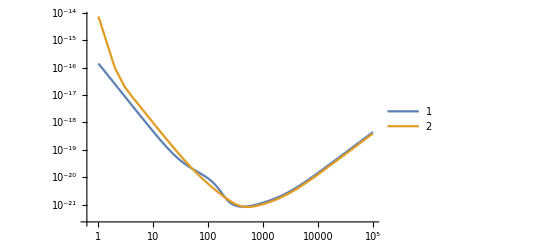

```mathematica
ListLogLogPlot[{LISAhnf,Masellisahnf},Joined->True,PlotLegends->Automatic, Frame->True,FrameTicks->{Automatic,{ticks,None}}]
```

### IMR coefficients

This section provides the analytical form of the IMRPhenomB coefficients derived from Ajith et. al (2011) (https://doi.org/10.1103/PhysRevLett.106.241101).

```mathematica
𝓍={{{-920.9,492.1,135},{6742,-1053,0},{-1.34*10^4,0,0}},
{{1.702 10^4,-9566,-2182},{-1.214*10^5,2.075 10^4,0},{2.386 10^5,0,0}},
{{-1.254*10^5,7.507 10^4,1.338 10^4},{8.735 10^5,-1.657*10^5,0},{-1.694*10^6,0,0}},
{{0,0,0},{0,0,0},{0,0,0}},
{{-8.898*10^5,6.31 10^5,5.068 10^4},{5.981 10^6,-1.415*10^6,0},{-1.128*10^7,0,0}},
{{8.696*10^5,-6.71*10^5,-3.008*10^4},{-5.838*10^6,1.514*10^6,0},{1.089*10^7,0,0}}};

ψ0[χ_]:={3715/756,-16π+113/3 χ,15293365/508032-405/8 χ^2,0,0,0};

𝓎={{{0.6437,0.827,-0.2706},     {-0.05822,-3.935,0},{-7.092,0,0}},
{{0.1469,-0.1228,-0.02609},{-0.0249,0.1701,0},   {2.325,0,0}},
{{-0.4098,-0.03523,0.1008},{1.829,-0.02017,0},   {-2.87,0,0}},
{{-0.1331,-0.08172,0.1451},{-0.2714,0.1279,0},   {4.922,0,0}}};

μ0[χ_]:={1-4.455(1-χ)^0.217+3.521(1-χ)^0.26,(1-0.63(1-χ)^0.3)/2,((1-0.63(1-χ)^0.3) (1-χ)^0.45)/4,0.3236+0.04894χ+0.01346χ^2};

α[η_,χ_]:={-(323/224)+451/168 η,(27/8-11/6 η)χ}; (* α2 and α3 *)

ϵ[χ_]:={1.4547χ-1.8897,-1.8153χ+1.6557}; (* ϵ1 and ϵ2 *)

ψ[k_,η_,χ_]:=ψ0[χ][[k]]+Sum[𝓍[[k,i,j+1]]η^i χ^j,{i,1,3},{j,0,Min[3-i,2]}];

Ψ[f_,M_,η_,χ_,tc_,ϕc_]:=2π f tc+ϕc+3/(128 η (π M f)^(5/3)) (1+Sum[(π M f)^(l/3) ψ[l-1,η,χ],{l,2,7}]);

μ[k_,η_,χ_]:=μ0[χ][[k]]+Sum[𝓎[[k,i,j+1]]η^i χ^j,{i,1,3},{j,0,Min[3-i,2]}];

𝒻1[M_,η_,χ_]:=μ[1,η,χ]/(M π);
𝒻2[M_,η_,χ_]:=μ[2,η,χ]/(M π);
𝒻3[M_,η_,χ_]:=μ[4,η,χ]/(M π);
σLor[M_,η_,χ_] :=μ[3,η,χ]/(M π);
```

```mathematica
𝒜i[f_,M_,η_,χ_]:=(f/𝒻1[M,η,χ])^(-7/6) (*(1+Sum[α[η,χ][[i-1]](π M f)^(i/3),{i,2,3}])*);

𝒜m[f_,M_,η_,χ_]:=(f/𝒻1[M,η,χ])^(-2/3) (*(1+Sum[ϵ[χ][[i]](π M f)^(i/3),{i,1,2}])*);

𝒜r[f_,M_,η_,χ_]:=1/(2π) σLor[M,η,χ]/((f-𝒻2[M,η,χ])^2+σLor[M,η,χ]^2/4);

wm[M_,η_,χ_]:=𝒜i[𝒻1[M,η,χ],M,η,χ]/𝒜m[𝒻1[M,η,χ],M,η,χ];

wr[M_,η_,χ_]:=wm[M,η,χ] 𝒜m[𝒻2[M,η,χ],M,η,χ]/𝒜r[𝒻2[M,η,χ],M,η,χ];
```

### Waveform template and dephasing

This section provides the waveform template constructed from the coefficients provided earlier.

#### Phase initializations

We initialize the dephasing factor, linear in the density of the surrounding medium and complete with the leading PN phase factor.

```mathematica
ϕenv[f_,ℳ_,ρ0_,index_]:=3/(128 (π ℳ f)^(5/3))(π ℳ f)^index*ρ0    (* index = -gamma in Cardoso and Maselli's paper *)
```

Next, we initialize the additional factors coming from Cardoso and Maselli’s Table 1.

```mathematica
kβdrag[m1_,m2_]=-η^-3(1-3η)π^(-11/3)//.η->(m1 m2)/(m1+m2)^2;
kβaccretion[m1_,m2_]=-η^-1 π^-3//.η->(m1 m2)/(m1+m2)^2;
```

The next four cells initialize some ψ_Dthat is added to the phase. (Maybe related to the detector?)

```mathematica
tpp[ν_]:={1,0,4/3(743/336+11/4 η)η^(-2/5),-(32π)/5 η^(-3/5),2(3058673/1016064+5429/1008 η+617/144 η^2)η^(-4/5),((13π)/3 η-(7729π)/252)η^-1};
tf=τ0-5/256 ℳ(π ℳ f)^(-8/3)Sum[tpp[ν][[i]](ℳ π f)^((i-1)/3),{i,1,4}];
ϕT=(2π)/T tf;
```

```mathematica
yr=3600*24*365*299792; (* in km *)
day=3600*24 299792; (* in km *)
RUA=1.495978707 10^8; (* in km *)
RE=6371; (* in km *)
T=1yr;
TE=1day;
```

```mathematica
ϕs=π/2;
θs=0;
{δ,eps}={39.,23.4}π/180;
ϕE=2π tf(1/TE-1/T);
θsT=ArcCos[Cos[θs](Cos[δ]Cos[eps]-Sin[δ]Sin[eps]Cos[ϕE])+Sin[θs](Cos[ϕs](Cos[δ]Cos[eps]+Sin[δ]Cos[eps]Cos[ϕE])-Sin[ϕs]Cos[δ]Sin[ϕE])];
```

```mathematica
ψD[ℳ_,η_,τ0_,f_]=2π f (RUA Sin[θs] Cos[ϕT-ϕs]+RE Cos[θsT]);
```

#### Waveform construction and plots

We then construct `hPhBppE`, or the IMRPhenomB strain e^(i (ψ_D-ψ_env-ψ_PN)) in parametrized Post-Einsteinian form (without the Newtonian amplitude from Berti et. al (2005) https://doi.org/10.1103/PhysRevD.71.084025)

```mathematica
hPhBppE[f_][ℳ_,η_,χ_,tc_,ϕc_,d_,ρ0_,index_]:=With[{M=η^(-3/5)ℳ},Exp[-I (ϕenv[f,ℳ,ρ0,index]+Ψ[f,M,η,χ,tc,ϕc])]]Exp[I ψD[ℳ,η,tc,f]]
```

```mathematica
hPhBppEVac[f_][ℳ_,η_,χ_,tc_,ϕc_,d_]:=With[{M=η^(-3/5)ℳ},Exp[-I (Ψ[f,M,η,χ,tc,ϕc])]]Exp[I ψD[ℳ,η,tc,f]]
```

```mathematica
hPhBppEpull[f_][ℳ_,η_,χ_,tc_,ϕc_,d_,ρ0_,γ_]:=With[{M=η^(-3/5)ℳ},Exp[-I (Ψ[f,M,η,χ,tc,ϕc]-(3/(128 (π ℳ f)^(5/3)) (M)^2 ((M) f)^-γ ρ0  G/cc^2))]]Exp[I ψD[ℳ,η,tc,f]];
hPhBppEdrag[f_][ℳ_,η_,χ_,tc_,ϕc_,d_,ρ0_,γ_]:=With[{M=η^(-3/5)ℳ},Exp[-I (Ψ[f,M,η,χ,tc,ϕc]-(3/(128 (π ℳ f)^(5/3)) (M)^2 ((M) f)^-γ ρ0 G/cc^2(-η^-3(1-3η)π^(-11/3))))]]Exp[I ψD[ℳ,η,tc,f]];
hPhBppEcolless[f_][ℳ_,η_,χ_,tc_,ϕc_,d_,ρ0_,γ_]:=With[{M=η^(-3/5)ℳ},Exp[-I (Ψ[f,M,η,χ,tc,ϕc]-(3/(128 (π ℳ f)^(5/3)) (M)^2 ((M) f)^-γ ρ0 G/cc^2(-η^-1 π^-3)))]]Exp[I ψD[ℳ,η,tc,f]];
```

We also construct the derivative function that consists of derivatives for the six source parameters listed by Cardoso and Maselli. This will be used for calculating the Fisher matrix elements.

```mathematica
dhdθ[f_,index_]= {ℳ D[hPhBppE[f][ℳ,η,χ,τ ,ϕ,d,ρ0,index],ℳ],
	 η D[hPhBppE[f][ℳ,η,χ,τ ,ϕ,d,ρ0,index],η],
	   D[hPhBppE[f][ℳ,η,χ,τ ,ϕ,d,ρ0,index],τ],
	   D[hPhBppE[f][ℳ,η,χ,τ ,ϕ,d,ρ0,index],ϕ],
	   D[hPhBppE[f][ℳ,η,χ,τ ,ϕ,d,ρ0,index],χ],
       D[hPhBppE[f][ℳ,η,χ,τ ,ϕ,d,ρ0,index],ρ0]};
```

The next two plots are checks for order of magnitude of the waveform and its derivative with respect to the surrounding density for an EMRI of central mass 10^5 M_sun and secondary mass of 10 M_sun.

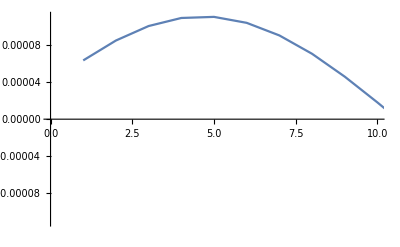

```mathematica
ListLinePlot[{Re[Table[With[{ℳ=398.099msun,η=0.00009998000299960005,χ=0.7999700029997,τ=0 ,ϕ=-Pi/4,d=1000,ρ0=p,index=-2,f=10^-5,C=Sqrt[5]},Evaluate[C (2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6)dhdθ[f,index][[-1]]]],{p,0,1000,1}]]},PlotRange->{{0,10},Automatic}]
```

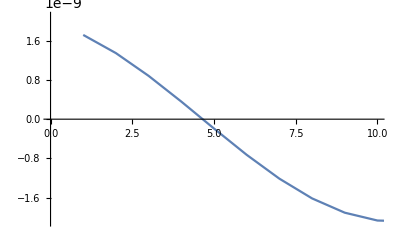

```mathematica
ListLinePlot[Re[Table[With[{ℳ=398.099msun,η=0.00009998000299960005,χ=0.7999700029997,τ=0 ,ϕ=-Pi/4,d=1000,ρ0=p,index=-2, C=Sqrt[5],f=10^-5},Evaluate[C (2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6)hPhBppE[f][ℳ,η,χ,τ,ϕ,d,ρ0,index]]],{p,0,1000,1}]],PlotRange->{{0,10},Automatic}]
```

We then visualize the waveforms in the frequency domain (including the amplitude) from their frequency 4 years before the merger up to ISCO for m_1= 10^5 M_sun, m_2 = 10 M_sun, χ_1=0.8, and χ_2=0.5. We create the vacuum waveform, as well as the dephased waveforms due to gravitational pull, gravitational drag, and collisionless accretion, for a surrounding density of 10^3 kg/m^3.

```mathematica
hptildefd=Re[Table[Evaluate[With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3}, Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEVac[f/cc][ℳ,η,χ,τ ,ϕ,d])]],{f,0.00328985,0.113325,10^-5}]];
hpgravfd=Re[Table[Evaluate[With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=2}, Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEpull[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])]],{f,0.00328985,0.113325,10^-5}]];
hpdragfd=Re[Table[Evaluate[With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=11/3}, Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEdrag[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])]],{f,0.00328985,0.113325,10^-5}]];
hpcollessfd=Re[Table[Evaluate[With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=3}, Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEcolless[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])]],{f,0.00328985,0.113325,10^-5}]];
```

```mathematica
hptildefd[f_]:=With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3}, Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEVac[f/cc][ℳ,η,χ,τ ,ϕ,d])];
hpgravfd[f_]:=With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=2}, Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEpull[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])];
hpdragfd[f_]:=With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=11/3}, Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEdrag[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])];
hpcollessfd[f_]:=With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=3}, Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEcolless[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])] ;(* in units of km^-1 *)
```

```mathematica
Re[hpcollessfd[10^-5]]
```

1.29414×10^-9

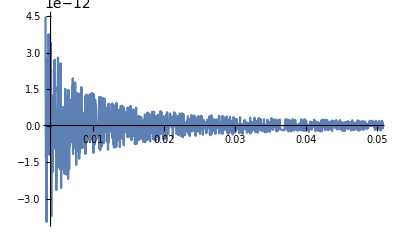

```mathematica
Plot[Re[hptildefd[f]]-Re[hpdragfd[f]],{f,0.00328985,0.113325},PlotRange->{{0.004,0.05},Full}]
```

We also create their corresponding characteristic strain h_c(f) in the frequency domain, for plotting with the noise characteristic amplitude h_n(f) (See Moore et. al (2015). https://doi.org/10.1088/0264-9381/32/1/015014 for the summary of the different waveform conventions)

```mathematica
hcfd=Re[Table[Evaluate[With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3}, 2 f/cc Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEVac[f/cc][ℳ,η,χ,τ ,ϕ,d])]],{f,0.0032898520426597314,0.11332458708398821,10^-5}]];
hcgravfd=Re[Table[Evaluate[With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=2}, 2 f/cc Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEpull[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])]],{f,0.0032898520426597314,0.11332458708398821,10^-5}]];
hcdragfd=Re[Table[Evaluate[With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=11/3}, 2 f/cc Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEdrag[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])]],{f,0.0032898520426597314,0.11332458708398821,10^-5}]];
hccollessfd=Re[Table[Evaluate[With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=3}, 2 f/cc Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEcolless[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])]],{f,0.0032898520426597314,0.11332458708398821,10^-5}]];
```

```mathematica
Length[hcfd]
```

11004

```mathematica
xticks=Table[{10^5 i,i},{i,0,0.0015,0.00025}]
```

{{0.,0.},{25.,0.00025},{50.,0.0005},{75.,0.00075},{100.,0.001},{125.,0.00125},{150.,0.0015}}

We see in this plot that the dephased waveforms deviate from the vacuum waveform at low frequencies, corresponding to their low and negative PN correction order.

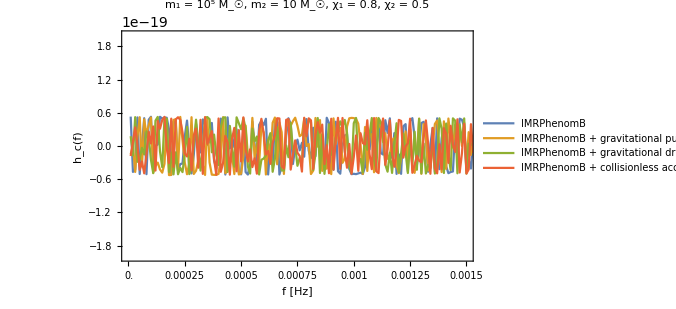

```mathematica
ListLinePlot[{hcfd,hcgravfd,hcdragfd,hccollessfd},FrameTicks->{{Automatic,None},{xticks,None}}, PlotRange->{{0,150},{-2*10^-19,2*10^-19}},ImageSize->500,Frame->True,Axes->False,FrameLabel->{{Style["h_c(f)",18],None},{Style["f [Hz]",18],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"CMU Serif",AbsoluteThickness[1]],PlotLegends->Placed[{Style["IMRPhenomB",Black,FontFamily->"CMU Sans Serif"],Style["IMRPhenomB + gravitational pull",Black,FontFamily->"CMU Sans Serif"],Style["IMRPhenomB + gravitational drag",Black,FontFamily->"CMU Sans Serif"],Style["IMRPhenomB + collisionless accretion",Black,FontFamily->"CMU Sans Serif"]},Scaled[{0.6,0.8}]],PlotLabel->Style["m_1 = 10^5 M_☉, m_2 = 10 M_☉, χ_1 = 0.8, χ_2 = 0.5",15,Black,FontFamily->"CMU Sans Serif",Italic]]
```

```mathematica
xlogticks=Table[{10^5 i,N[i]},{i,{10^-5,10^-4,10^-3,10^-2,10^-1,1}}]
```

{{1,0.00001},{10,0.0001},{100,0.001},{1000,0.01},{10000,0.1},{100000,1.}}

The next plot shows Maselli’s |h_n(f)|^2 and the waveforms’ |h_c(f)|^2 created earlier, plotted in a log-log scale. Compare with Kocsis et. al’s Figure 8 in Kocsis et. al (2011). https://doi.org/10.1103/PhysRevD.84.024032

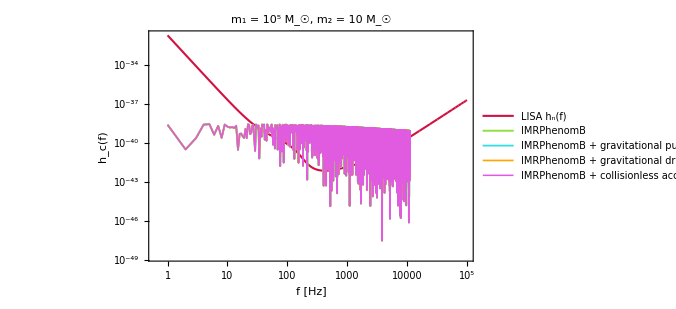

```mathematica
ListLogLogPlot[{(Abs[LISAhnf])^2,(Abs[hcfd])^2,(Abs[hcgravfd])^2,(Abs[hcdragfd])^2,(Abs[hccollessfd])^2},Joined->True,FrameTicks->{Automatic,{xlogticks,None}}, PlotRange->{Automatic,Automatic},ImageSize->500,Frame->True,Axes->False,FrameLabel->{{Style["h_c(f)",18],None},{Style["f [Hz]",18],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"CMU Serif",AbsoluteThickness[1]],GridLines->{{{11004,Directive[Black,Thick,Dashed]}}, None},PlotLegends->Placed[{Style["LISA h_n(f)",Black,FontFamily->"CMU Sans Serif"],Style["IMRPhenomB",Black,FontFamily->"CMU Sans Serif"],Style["IMRPhenomB + gravitational pull",Black,FontFamily->"CMU Sans Serif"],Style["IMRPhenomB + gravitational drag",Black,FontFamily->"CMU Sans Serif"],Style["IMRPhenomB + collisionless accretion",Black,FontFamily->"CMU Sans Serif"]},Scaled[{0.35,0.25}]],PlotStyle->{Directive[C2,AbsoluteThickness[1.5]],Directive[C7,AbsoluteThickness[1.4]],Directive[C5,AbsoluteThickness[1.3]],Directive[C4,AbsoluteThickness[1.2]],Directive[C9,AbsoluteThickness[1.1]]},ImagePadding->{{75,55},{75,10}},PlotLabel->Style["m_1 = 10^5 M_☉, m_2 = 10 M_☉",18,Black,FontFamily->"CMU Sans Serif"]]
```

### SNR

```mathematica
dephase[𝒹_,m1_,m2_,χeff_,t_,env_,γ_,ρ0_]:=Block[{ℳ,η,q=m1/m2,d,τ,ϕ,χ, 𝒽1,𝒽2,
𝒫,i,j,fmin,fmax,f,IscoS,𝒯,𝒩,amp,M=m1+m2,ψenv,phivac,dephasing},

Off[NIntegrate::slwcon];
Off[NIntegrate::eincr];

(* ---- Binary parameters q = m1/m2 ≥ 1 ---- *)
{ℳ,η,τ,ϕ,χ,d} = {(q/(1+q)^2)^(3/5)msun (M),q/(1+q)^2,0,-π/4,χeff,𝒹};
 
(* ---- Time of observation in terms of 4 months; 4 years = 12x 4 months = 48 months ---- *)
𝒯=t/3;
ψenv[f_]=Which[env=="pull",3/(128 (π ℳ f)^(5/3))(M)^2((M)f)^-γ ρ0 G/cc^2,
env=="drag",3/(128 (π ℳ f)^(5/3))(M)^2((M)f)^-γ kβdrag[m1,m2]ρ0 G/cc^2,env=="colless",3/(128 (π ℳ f)^(5/3))(M)^2((M)f)^-γ kβaccretion[m1,m2]ρ0 G/cc^2];

IscoS=cc 𝒻1[(M)msun,η,χ]+0cc/(π 6^(3/2)(M)msun); (* in Hz *)
phivac[f_] =ψD[ℳ,η,τ,f]-Ψ[f,M,η,χ,τ,ϕ]; (* dimless *)
(* 𝒽2[f_] =amp[f] hPhBppEVac[f/cc][ℳ,η,χ,τ,ϕ,d]*Exp[-I ψenv[f/cc]]; *)

fmin = Max[10^-5,4.149 10^-5 (ℳ/msun 10^-6)^(-5/8) 𝒯^(-3/8)];
fmax = Min[1,IscoS];

dephasing = Sqrt[𝒪[LISA[f],phivac[f]-ψenv[f],phivac[f]-ψenv[f],fmin,fmax]];
(* Print["f_min = ",fmin," -- f_max = ", fmax]; *)
Return[dephasing]
]
```

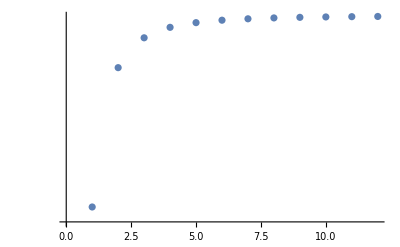

```mathematica
ListLogPlot[Table[dephase[1000,10^6,10,(10^6*0.8+10*0.5)/(10^6+10),t,"pull",2,1000],{t,1,12}]]
```

```mathematica
SNR[𝒹_,m1_,m2_,χeff_,t_]:=Block[{ℳ,η,q=m1/m2,d,τ,ϕ,χ, 𝒽1,𝒽2,
	ρ,C,𝒫,i,j,fmin,fmax,f,IscoS,𝒯,𝒩,amp,M=m1+m2},

Off[NIntegrate::slwcon];
Off[NIntegrate::eincr];

C=√5;

(* ---- Binary parameters q = m1/m2 ≥ 1 ---- *)
{ℳ,η,τ,ϕ,χ,d} = {(q/(1+q)^2)^(3/5)msun (M),q/(1+q)^2,0,-π/4,χeff,𝒹};
 
(* ---- Time of observation in terms of 4 months; 4 years = 12x 4 months = 48 months ---- *)
𝒯=t/3;

IscoS=cc 𝒻1[(M)msun,η,χ]+0cc/(π 6^(3/2)(M)msun); (* in Hz *)
amp[f_]=C (2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6);
𝒽1[f_] =amp[f] hPhBppEVac[f/cc][ℳ,η,χ,τ,ϕ,d]; (* in km *)
(* 𝒽2[f_] =amp[f] hPhBppEVac[f/cc][ℳ,η,χ,τ,ϕ,d]*Exp[-I ψenv[f/cc]]; *)

fmin = Max[10^-5,4.149 10^-5 (ℳ/msun 10^-6)^(-5/8) 𝒯^(-3/8)];
fmax = Min[1,IscoS];

ρ = Sqrt[𝒪[LISA[f],𝒽1[f],𝒽1[f],fmin,fmax]];
(* Print["f_min = ",fmin," -- f_max = ", fmax]; *)
Return[ρ]
]
```

```mathematica
SNRvac=Join[{SNR[1000,10^6,10,(10^6*0.8+10*0.5)/(10^6+10),0.25]},Table[SNR[1000,10^6,10,(10^6*0.8+10*0.5)/(10^6+10),t],{t,1,12}]]
```

{56.0531275570995981914926479965,102.898399967414978274816206581,121.008691671773733544109622287,128.8500285993948092617510843,133.159737660039161486282533846,135.85879832422412074377691391,137.696997821001817298596507731,139.024282833519586619734205082,140.02482934468459855342133049,140.804384143869969894912327431,141.427815591546047426510532475,141.937041171170986113754720737,142.360309715156605687340226898}

```mathematica
Get["SNRcollesstimenew.m"]
Get["SNRdragtimenew.m"]
```

Is this plot telling us that the SNR of the waveform difference is inherently higher because we’re only comparing phases and not amplitudes?

```mathematica
ListLogPlot[{SNRvac,SNRcollesstimenew[[6]]},PlotLegends->Automatic]
```

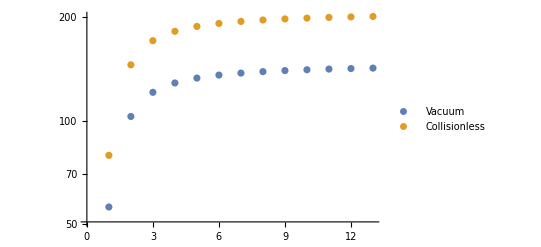

```mathematica
ψenv[f_][m1_,m2_,ρ0_,γ_,env_]:=Which[env=="pull",3/(128 (π ℳ f)^(5/3))(m1+m2)^2((m1+m2)f)^-γ ρ0 G/cc^2,
env=="drag",3/(128 (π ℳ f)^(5/3))(m1+m2)^2((m1+m2)f)^-γ kβdrag[m1,m2]ρ0 G/cc^2,env=="colless",3/(128 (π ℳ f)^(5/3))(m1+m2)^2((m1+m2)f)^-γ kβaccretion[m1,m2]ρ0 G/cc^2]//. ℳ-> (m1 m2/m1+m2)^(3/5)*(m1+m2)^(2/5) (* density is in kg/m^3 *)
```

```mathematica
ψenv[f/cc][10^5 msun,10 msun,10^3,2,"pull"]
ψenv[f/cc][10^5 msun,10 msun,10^3,3,"colless"]
ψenv[f/cc][10^5 msun,10 msun,10^3,11/3,"drag"]
```

(3.77479×10^-6)/f^(11/3)

-0.00247164/f^(14/3)

-184742./f^(16/3)

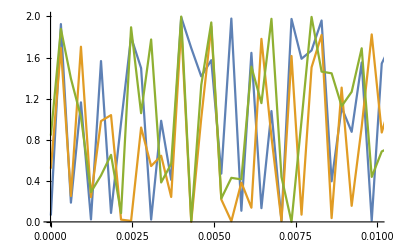

```mathematica
Plot[{1-Cos[ψenv[f/cc][10^6 msun,10 msun,10^3,2,"pull"]],1-Cos[ψenv[f/cc][10^6 msun,10 msun,10^3,3,"colless"]],1-Cos[ψenv[f/cc][10^6 msun,10 msun,10^3,11/3,"drag"]]},{f,10^-5,1},PlotRange->{{0,10^-2},Full}]
```

```mathematica
𝒪[LISA[f],1-Cos[ψenv[f/cc][10^6 msun,10 msun,10^3,2,"pull"]],1,0.00185,0.0113276]
𝒪[LISA[f],1-Cos[ψenv[f/cc][10^6 msun,10 msun,10^3,3,"colless"]],1,0.00185,0.0113276]
𝒪[LISA[f],1-Cos[ψenv[f/cc][10^6 msun,10 msun,10^3,11/3,"drag"]],1,0.00185,0.0113276]
```

2.8282238144457987911413042078×10^27

2.93279639798429916067888658167×10^27

2.93279551381811598028986848354×10^27

```mathematica
NIntegrate[1-Cos[ψenv[f/cc][10^6,10,10^3,11/3,"drag"]],{f,0.00185,0.0113276}]
```

0.0094776

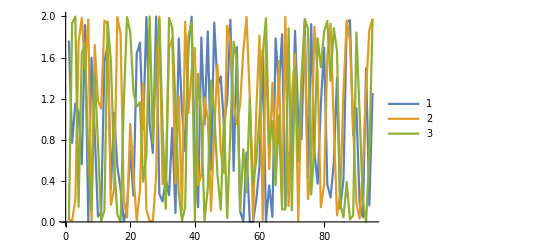

```mathematica
ListLinePlot[{Table[1-Cos[ψenv[f/cc][10^6,10,10^3,11/3,"drag"]],{f,0.00185,0.0113276
,10^-4}],Table[1-Cos[ψenv[f/cc][10^6,10,10^3,2,"pull"]],{f,0.00185,0.0113276
,10^-4}],Table[1-Cos[ψenv[f/cc][10^6,10,10^3,3,"colless"]],{f,0.00185,0.0113276
,10^-4}]},PlotLegends->Automatic]
```

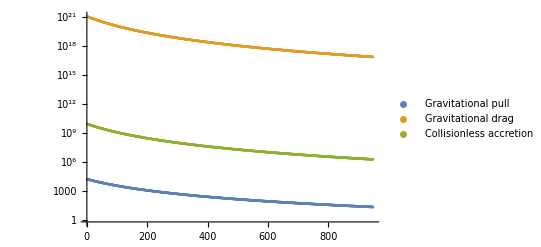

To create the Fisher matrix and calculate the SNRs for each waveform, we first start with the overlap integral ∫(h_1*h_2^*)/(S_n(f))ⅆf, where the integral runs from max[10^5, f_4] where f_4 is the frequency of the binary 4 years before the merger, up to min[1, f_ISCO], where f_ISCO is the frequency at ISCO coming from Ajith’s transition frequency f_(I-M).

```mathematica
𝒪[Noise_,h1_,h2_,fI_,fE_]:=4Re[NIntegrate[SetPrecision[h1*Conjugate[h2]
	/(Noise cc^2),40],{f,fI,fE},MaxRecursion->50,PrecisionGoal->25,AccuracyGoal->23,WorkingPrecision->30]];
```

We then calculate SNR of the waveform difference (vacuum - dephased), following Kocsis et. al’s equation 22 (same paper as earlier). This function accepts the following inputs in order: the distance of the binary, masses of the primary and secondary body, effective spin χ_eff= (χ_1 m_1+ χ_2 m_2)/(m_1+m_2), index (-γ, specific to each environmental effect tabulated in Cardoso and Maselli’s Table 1), time of observation (in terms of 4 months to lessen calculations, i.e. t = 12 corresponds to 4 years of observation), density of the surrounding medium (in kg/m^3), and the specific environmental effect (for choosing the appropriate dephasing factor).

```mathematica
SNRdifftry[𝒹_,m1_,m2_,χeff_,index_,t_,ρ0_,env_]:=Block[{ℳ,η,q=m1/m2,d,τ,ϕ,χ, 𝒽1,𝒽2,
	ρ,C,𝒫,i,j,fmin,fmax,f,IscoS,𝒯,𝒩,amp,ψenv,γ=-index,M=m1+m2},

Off[NIntegrate::slwcon];
Off[NIntegrate::eincr];

C=√5;

(* ---- Binary parameters q = m1/m2 ≥ 1 ---- *)
{ℳ,η,τ,ϕ,χ,d} = {(q/(1+q)^2)^(3/5)msun (M),q/(1+q)^2,0,-π/4,χeff,𝒹};
 
(* ---- Time of observation in terms of 4 months; 4 years = 12x 4 months = 48 months ---- *)
𝒯=t/3;

ψenv[f_]=Which[env=="pull",3/(128 (π ℳ f)^(5/3))(M)^2((M)f)^-γ ρ0 G/cc^2,
env=="drag",3/(128 (π ℳ f)^(5/3))(M)^2((M)f)^-γ kβdrag[m1,m2]ρ0 G/cc^2,env=="colless",3/(128 (π ℳ f)^(5/3))(M)^2((M)f)^-γ kβaccretion[m1,m2]ρ0 G/cc^2];

IscoS=cc 𝒻1[(M)msun,η,χ]+0cc/(π 6^(3/2)(M)msun); (* in Hz *)
amp[f_]=C (2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6);
𝒽1[f_] =amp[f] hPhBppEVac[f/cc][ℳ,η,χ,τ,ϕ,d]; (* in km *)
(* 𝒽2[f_] =amp[f] hPhBppEVac[f/cc][ℳ,η,χ,τ,ϕ,d]*Exp[-I ψenv[f/cc]]; *)

fmin = Max[10^-5,4.149 10^-5 (ℳ/msun 10^-6)^(-5/8) 𝒯^(-3/8)];
fmax = Min[1,IscoS];

ρ = Sqrt[2𝒪[LISA[f],𝒽1[f](1-Cos[ψenv[f/cc]]),𝒽1[f],fmin,fmax]];
(* Print["f_min = ",fmin," -- f_max = ", fmax]; *)
Return[ρ]
]
```

Sample SNR calculations

```mathematica
drag1mo=Monitor[Table[SNRdiff[1000,m1,10,(m1*0.8+10*0.5)/(m1+10),-11/3,0.25,1000,"drag"],{m1,{10^2,10^3,10^4,10^5,10^6}}],N[m1]];
colless1mo=Monitor[Table[SNRdiff[1000,m1,10,(m1*0.8+10*0.5)/(m1+10),-3,0.25,1000,"colless"],{m1,{10^2,10^3,10^4,10^5,10^6}}],N[m1]];
```

```mathematica
drag1mo//TableForm
```

0.258292281865196814164317318111
1.41714178966542873584895263028
6.96140373200126453336058021164
29.9790871352239116964256462574
79.2710932046793254892874508538

```mathematica
SNRpulltimenew=Join[Take[SNRpulltime,All,{1,-1,4}],Transpose[{SNRpulltime[[All,-1]]}],2];
```

```mathematica
months=Join[{1},Table[4i,{i,1,12}]]
```

{1,4,8,12,16,20,24,28,32,36,40,44,48}

```mathematica
SNRpulltimenew=Join[{months},SNRpulltimenew];
SNRpulltimenew//TableForm
```

1 | 4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
0.241753746244640399381985439306 | 0.66536139255880840936696051534 | 0.923219361819249388403927737839 | 1.12149505973861066113265892402 | 1.28805054058982182230119070602 | 1.43432544140837641462138546995 | 1.56315236785823192111181813917 | 1.68042351488652107191780724672 | 1.78732312426730970744548869277 | 1.88656989865938805670388600704 | 1.97922255878502517258995370752 | 2.06474836771351778096482219727 | 2.12624518989909608962182464382
1.3718485669561560782472280323 | 3.33672303533301414554227009479 | 4.41124907461135836440356325919 | 5.20769461713302565597941888291 | 5.84410361569014098258638843671 | 6.37920289255101086712997367506 | 6.84347953951868702781222122821 | 7.25642366369750066502892218339 | 7.62973973533474037021098931507 | 7.96900750412398887080396374885 | 8.28109753666331521518704395588 | 8.57102779540907330737596989136 | 8.77584699186805424404250138701
6.81624847074674832756346153219 | 14.3094234410574464537787523097 | 18.0016050711355833865772063863 | 20.550327279297320084385270926 | 22.5498448498104479338449985769 | 24.1809451460392227536562351466 | 25.5786228492625327285481540791 | 26.7863933883126559259374309664 | 27.8568165400048093513342217369 | 28.8158022927078016313607415382 | 29.6799316848113135788587146029 | 30.4648842679553832075935918168 | 31.0117264172415894837505726213
29.6475330413105980041897337304 | 53.685240352918681397965776221 | 64.1982482720204401697321678807 | 70.8727196050762417611250666063 | 75.6473276360688332822442021853 | 79.2513272401751527594091977235 | 82.0612187169576057537177626909 | 84.3230974009063544505094258719 | 86.1755335520216958475995700744 | 87.7212007634495806005132216568 | 89.0234967169345034601018396499 | 90.1385772811990482076308743961 | 90.8753733647964826886430417988
78.6381570897424626731507269645 | 154.494601737612255458273765745 | 174.590248775108147517729859389 | 183.978347278572065133878709239 | 189.353253026836618618641518773 | 192.80203467223327643531302557 | 195.186380252825932281647464288 | 196.930285246175322871866008809 | 198.256902429063918959893315995 | 199.297098378380242291665794195 | 200.133726675708430170005916166 | 200.820913892431672025034587717 | 201.25929523567811751598157499

```mathematica
SNRdragtimenew//TableForm
```

1 | 4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
0.258292281865196814164317318111 | 0.586111851499010907638253388743 | 0.86485112697394552154776441724 | 1.07592278544203265957206365735 | 1.2501940210400984977547276701 | 1.40039600679187759547279049894 | 1.53330471362588272169475487051 | 1.65304426563530835154919553259 | 1.76234655534280798628930225095 | 1.86313094436188687521872971348 | 1.95680589619555850642718153072 | 2.04444026288017161958560609163 | 2.12686717104346230807786538386
1.41714178966542873584895263028 | 2.99031492707845019327739017265 | 4.18608249762367342487019568723 | 5.03050549637289828439483161132 | 5.69739204343509784464988677911 | 6.25417421314536867549324327242 | 6.73500324034593102298658636464 | 7.15982925452407143646347655732 | 7.54141935751763101117053709945 | 7.88848316280574302714655688938 | 8.20725145772855741006692703298 | 8.50234886732047129280651180922 | 8.77731036209284457965463734053
6.96140373200126453336058021164 | 13.1017782657767996930129047714 | 17.240456630966551142672831678 | 20.0001626289398074557549351578 | 22.1055033419278899383679692783 | 23.817545363075650599900288947 | 25.2629816473642327407033190046 | 26.5138282968632653685803697751 | 27.6153477075162535536895801053 | 28.598054176285650560666555146 | 29.4836164038857656544135077709 | 30.2880512643288480448670561027 | 31.0235816069545355256335724271
29.9790871352239116964256462574 | 50.0585433263560277716703545228 | 62.1694218391379856951902622325 | 69.5428935868960660870565859802 | 74.6941245825796972558594652358 | 78.5349697412573564714667951666 | 81.5157755695442187065658570098 | 83.8954553436936500814307181257 | 85.836803582778533959056958724 | 87.4483981896643740630587888459 | 88.8057809804561899033189486296 | 89.9632308639418164110631245758 | 90.9607677968180673472857920642
79.2710932046793254892874508538 | 145.520312780409503903589325854 | 171.132132927246610286024981673 | 182.221457957425311947137928363 | 188.316306960870766434460292857 | 192.133355157828869663287071594 | 194.732961816519286561348298009 | 196.61002628235645916791928167 | 198.025012728231102413926058036 | 199.127469697852089152977762582 | 200.009134906365490567572520489 | 200.729288627378379275006550916 | 201.327880742808755407052895261

```mathematica
SNRcollesstimenew//TableForm
```

1 | 4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
0.258306014676815693792358122112 | 0.586118105760792274405478918868 | 0.864855204871729045075059886951 | 1.07592613774885553975034923171 | 1.25019690699727800237849756925 | 1.40039857645521161117173078865 | 1.53330705299402312201928974797 | 1.65304643034390268955762546613 | 1.76234857498091924295684290816 | 1.86313286582449119243423162461 | 1.95680771797336457495221054463 | 2.04444201807282648477728659652 | 2.12686885063093275729720825385
1.41712921103183544629833888627 | 2.99030882697629019567511621857 | 4.1860783513501164442158481318 | 5.0305019571660253607655937778 | 5.69738893082806409531646631399 | 6.25417140432027674048232249628 | 6.73500065201019853931590129981 | 7.15982679886379062767200666657 | 7.54141702193333544888726096198 | 7.88848094540538868057690825811 | 8.20724931104761362623567599559 | 8.50234681039696600267458716158 | 8.7773083680950651961511557707
6.96131996481269470775728293312 | 13.101732819016386564574515121 | 17.2404220690297786248885099801 | 20.0001328727887502319308349277 | 22.1054764300279847050960255069 | 23.8175204205927513132398130437 | 25.2629581172872303486535752848 | 26.5138058848250129490629757321 | 27.6153261983761033969939625942 | 28.5980333892612737433757486161 | 29.48359624231977412916414358 | 30.2880316446533029793911188646 | 31.0235624502290902900142300302
29.9791581991173109645471856387 | 50.058585396832711718614061409 | 62.1694555276478302364942664919 | 69.5429236587385684259061735959 | 74.6941526305185379447755345196 | 78.5349963889928447839610041448 | 81.5158012509469056690157358844 | 83.8954802929345041720125383051 | 85.8368279767234158695442217502 | 87.4484221269580354355477916514 | 88.8058045563682748711243663186 | 89.963254132266262434122955678 | 90.960790813079497777201973469
79.2711053215055394404458533682 | 145.520317975670521545150970226 | 171.132137243575797004018026909 | 182.221462004367091395656092357 | 188.316310854271115266048865996 | 192.133358977316338955402116337 | 194.732965592365129986042937802 | 196.610030017815937362879153346 | 198.02501643970244260896350019 | 199.127473386868269438348214932 | 200.009138579521368747118834425 | 200.729292287679843770660661158 | 201.32788439182174673858348131

```mathematica
SNRdragtimenew=Join[{months},SNRdragtimenew];
SNRcollesstimenew=Join[{months},SNRcollesstimenew];
SNRdragtimenew//TableForm
SNRcollesstimenew//TableForm
```

```mathematica
Export["SNRpulltimenew.h5",SNRpulltimenew]
Export["SNRdragtimenew.h5",SNRdragtimenew]
Export["SNRcollesstimenew.h5",SNRcollesstimenew]
```

SNRdragtimenew.h5

SNRcollesstimenew.h5

```mathematica
SNRdragtimenew//MatrixForm
```

(1 | 4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
0.258292281865196814164317318111 | 0.586111851499010907638253388743 | 0.86485112697394552154776441724 | 1.07592278544203265957206365735 | 1.2501940210400984977547276701 | 1.40039600679187759547279049894 | 1.53330471362588272169475487051 | 1.65304426563530835154919553259 | 1.76234655534280798628930225095 | 1.86313094436188687521872971348 | 1.95680589619555850642718153072 | 2.04444026288017161958560609163 | 2.12686717104346230807786538386
1.41714178966542873584895263028 | 2.99031492707845019327739017265 | 4.18608249762367342487019568723 | 5.03050549637289828439483161132 | 5.69739204343509784464988677911 | 6.25417421314536867549324327242 | 6.73500324034593102298658636464 | 7.15982925452407143646347655732 | 7.54141935751763101117053709945 | 7.88848316280574302714655688938 | 8.20725145772855741006692703298 | 8.50234886732047129280651180922 | 8.77731036209284457965463734053
6.96140373200126453336058021164 | 13.1017782657767996930129047714 | 17.240456630966551142672831678 | 20.0001626289398074557549351578 | 22.1055033419278899383679692783 | 23.817545363075650599900288947 | 25.2629816473642327407033190046 | 26.5138282968632653685803697751 | 27.6153477075162535536895801053 | 28.598054176285650560666555146 | 29.4836164038857656544135077709 | 30.2880512643288480448670561027 | 31.0235816069545355256335724271
29.9790871352239116964256462574 | 50.0585433263560277716703545228 | 62.1694218391379856951902622325 | 69.5428935868960660870565859802 | 74.6941245825796972558594652358 | 78.5349697412573564714667951666 | 81.5157755695442187065658570098 | 83.8954553436936500814307181257 | 85.836803582778533959056958724 | 87.4483981896643740630587888459 | 88.8057809804561899033189486296 | 89.9632308639418164110631245758 | 90.9607677968180673472857920642
79.2710932046793254892874508538 | 145.520312780409503903589325854 | 171.132132927246610286024981673 | 182.221457957425311947137928363 | 188.316306960870766434460292857 | 192.133355157828869663287071594 | 194.732961816519286561348298009 | 196.61002628235645916791928167 | 198.025012728231102413926058036 | 199.127469697852089152977762582 | 200.009134906365490567572520489 | 200.729288627378379275006550916 | 201.327880742808755407052895261)

```mathematica
SNRdragtimenew=Join[Transpose[{drag1mo}],SNRdragtime,2];
SNRcollesstimenew=Join[Transpose[{colless1mo}],SNRcollesstime,2];
DumpSave["SNRdragtimenew.m",SNRdragtimenew]
DumpSave["SNRcollesstimenew.m",SNRcollesstimenew]
```

```mathematica
Monitor[SNRdragtime=Table[SNRdiff[1000,m1,10,(m1*0.8+10*0.5)/(m1+10),-11/3,t,1000,"drag"],{m1,{10^2,10^3,10^4,10^5,10^6}},{t,1,12}],t];
DumpSave["SNRdragtime.m",SNRdragtime]
Monitor[SNRcollesstime=Table[SNRdiff[1000,m1,10,(m1*0.8+10*0.5)/(m1+10),-3,t,1000,"colless"],{m1,{10^2,10^3,10^4,10^5,10^6}},{t,1,12}],t];
DumpSave["SNRcollesstime.m",SNRcollesstime]
```

```mathematica
Get["SNRpulltimenew.m"]
Get["SNRdragtimenew.m"]
Get["SNRcollesstimenew.m"]
```

We then plot the SNRs of the waveform differences for 5 binaries with different primary masses, each with a surrounding medium of density 10^3 kg/m^3, as well as the different environmental effects listed. The plot starts from 1 month of observation up to 4 years. We include a marker for SNR=10 which denotes the conservative value for detection. Thus, above this limit, the differences between using a vacuum waveform and environmentally-dephased waveform would be visible.

```mathematica
monthsticks=Table[{i,SNRpulltimenew[[1,i]]},{i,1,13}]
```

{{1,1},{2,4},{3,8},{4,12},{5,16},{6,20},{7,24},{8,28},{9,32},{10,36},{11,40},{12,44},{13,48}}

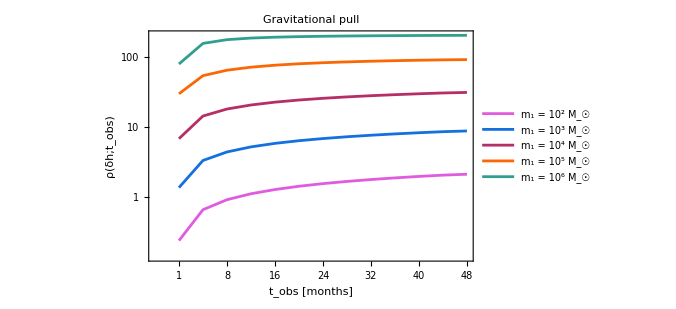

```mathematica
ListLogPlot[{SNRpulltimenew[[2]],SNRpulltimenew[[3]],SNRpulltimenew[[4]],SNRpulltimenew[[5]], SNRpulltimenew[[6]]},Joined->True,FrameTicks->{Automatic,{monthsticks,None}}, PlotRange->Automatic,ImageSize->500,Frame->True,Axes->False,FrameLabel->{{Style["ρ(δh;t_obs)",18],None},{Style["t_obs [months]",18],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"CMU Serif",AbsoluteThickness[1]],GridLines->{None, {{10,Directive[GrayLevel[0],Thick,Dashed]}}},PlotLegends->Placed[{Style["m_1 = 10^2 M_☉",Black,FontFamily->"CMU Serif"],Style["m_1 = 10^3 M_☉",Black,FontFamily->"CMU Serif"],Style["m_1 = 10^4 M_☉",Black,FontFamily->"CMU Serif"],Style["m_1 = 10^5 M_☉",Black,FontFamily->"CMU Serif"],Style["m_1 = 10^6 M_☉",Black,FontFamily->"CMU Serif"]},Scaled[{0.8,0.3}]],PlotStyle->{Directive[C9,AbsoluteThickness[2]],Directive[C10,AbsoluteThickness[2]],Directive[C11,AbsoluteThickness[2]],Directive[C12,AbsoluteThickness[2]],Directive[C13,AbsoluteThickness[2]]},ImagePadding->{{75,55},{75,10}},PlotLabel->Style["Gravitational pull",18,Black,FontFamily->"CMU Sans Serif"]]
```

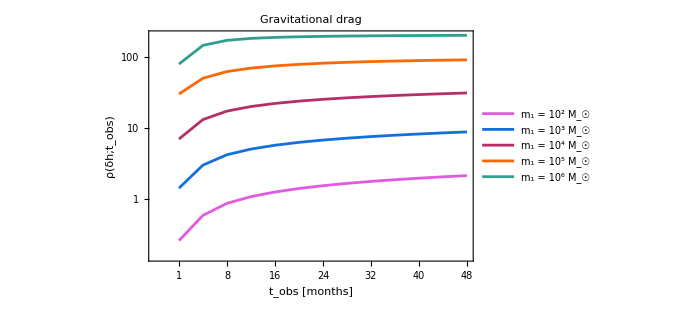

```mathematica
ListLogPlot[{SNRdragtimenew[[2]],SNRdragtimenew[[3]],SNRdragtimenew[[4]],SNRdragtimenew[[5]], SNRdragtimenew[[6]]},Joined->True,FrameTicks->{Automatic,{monthsticks,None}}, PlotRange->Automatic,ImageSize->500,Frame->True,Axes->False,FrameLabel->{{Style["ρ(δh;t_obs)",18],None},{Style["t_obs [months]",18],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"CMU Serif",AbsoluteThickness[1]],GridLines->{None, {{10,Directive[GrayLevel[0],Thick,Dashed]}}},PlotLegends->Placed[{Style["m_1 = 10^2 M_☉",Black,FontFamily->"CMU Serif"],Style["m_1 = 10^3 M_☉",Black,FontFamily->"CMU Serif"],Style["m_1 = 10^4 M_☉",Black,FontFamily->"CMU Serif"],Style["m_1 = 10^5 M_☉",Black,FontFamily->"CMU Serif"],Style["m_1 = 10^6 M_☉",Black,FontFamily->"CMU Serif"]},Scaled[{0.8,0.3}]],PlotStyle->{Directive[C9,AbsoluteThickness[2]],Directive[C10,AbsoluteThickness[2]],Directive[C11,AbsoluteThickness[2]],Directive[C12,AbsoluteThickness[2]],Directive[C13,AbsoluteThickness[2]]},ImagePadding->{{75,55},{75,10}},PlotLabel->Style["Gravitational drag",18,Black,FontFamily->"CMU Sans Serif"]]
```

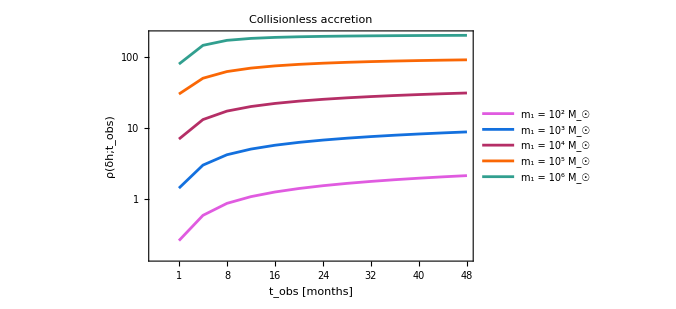

```mathematica
ListLogPlot[{SNRcollesstimenew[[2]],SNRcollesstimenew[[3]],SNRcollesstimenew[[4]],SNRcollesstimenew[[5]], SNRcollesstimenew[[6]]},Joined->True,FrameTicks->{Automatic,{monthsticks,None}}, PlotRange->Automatic,ImageSize->500,Frame->True,Axes->False,FrameLabel->{{Style["ρ(δh;t_obs)",18],None},{Style["t_obs [months]",18],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"CMU Serif",AbsoluteThickness[1]],GridLines->{None, {{10,Directive[GrayLevel[0],Thick,Dashed]}}},PlotLegends->Placed[{Style["m_1 = 10^2 M_☉",Black,FontFamily->"CMU Serif"],Style["m_1 = 10^3 M_☉",Black,FontFamily->"CMU Serif"],Style["m_1 = 10^4 M_☉",Black,FontFamily->"CMU Serif"],Style["m_1 = 10^5 M_☉",Black,FontFamily->"CMU Serif"],Style["m_1 = 10^6 M_☉",Black,FontFamily->"CMU Serif"]},Scaled[{0.8,0.3}]],PlotStyle->{Directive[C9,AbsoluteThickness[2]],Directive[C10,AbsoluteThickness[2]],Directive[C11,AbsoluteThickness[2]],Directive[C12,AbsoluteThickness[2]],Directive[C13,AbsoluteThickness[2]]},ImagePadding->{{75,55},{75,10}},PlotLabel->Style["Collisionless accretion",18,Black,FontFamily->"CMU Sans Serif"]]
```

We also try to plot the SNR as a function of different densities, just to check the optimum density for the gravitational pull effect.

```mathematica
Monitor[SNRpulldensity=Table[SNRdiff[1000,10^5,10,(10^5*0.8+10*0.5)/(10^5+10),-2,48,rho,"pull"],{rho,{1,10,100,1000,10000,100000,10^6,10^7,10^8,10^9}}],rho];
```

```mathematica
ticks=Table[{i,N[10^(i-1)]},{i,1,10}];
```

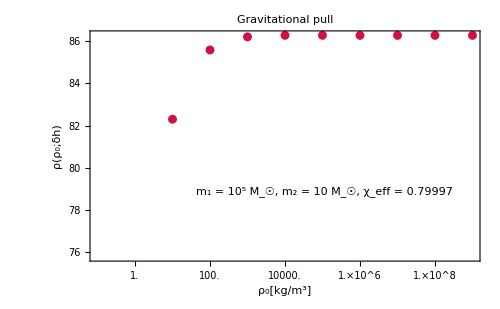

```mathematica
ListPlot[SNRpulldensity,Joined->False,FrameTicks->{Automatic,{ticks,None}}, PlotRange->Automatic,ImageSize->500,Frame->True,Axes->False,FrameLabel->{{Style["ρ(ρ_0;δh)",18],None},{Style["ρ_0[kg/m^3]",18],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"CMU Serif",AbsoluteThickness[1]],PlotLegends->Placed[Style["m_1 = 10^5 M_☉, m_2 = 10 M_☉, χ_eff = 0.79997",Black,FontFamily->"CMU Serif"],Scaled[{0.6,0.3}]],PlotStyle->Directive[C2,AbsoluteThickness[1.5]],ImagePadding->{{75,55},{75,10}},PlotLabel->Style["Gravitational pull",18,Black,FontFamily->"CMU Sans Serif"]]
```

Just a check to see how the phase varies with frequency:

```mathematica
ψenv[f_][m1_,m2_,env_,γ_,ρ0_]:=With[{ℳ=((m1/m2)/(1+m1/m2)^2)^(3/5)msun (m1+m2),M=m1+m2},Which[env=="pull",3/(128 (π ℳ f)^(5/3))(M)^2((M)f)^-γ ρ0 G/cc^2,
env=="drag",3/(128 (π ℳ f)^(5/3))(M)^2((M)f)^-γ kβdrag[m1,m2]ρ0 G/cc^2,env=="colless",3/(128 (π ℳ f)^(5/3)) (M)^2 ((M) f)^-γ kβaccretion[m1,m2]ρ0]]
```

```mathematica
psipull=NIntegrate[ψenv[f/cc][10^5,10,"pull",2,100],{f,4.149 10^-5 (398.099/msun 10^-6)^(-5/8) 4^(-3/8),1}];
psidrag=NIntegrate[ψenv[f/cc][10^5,10,"drag",11/3,100],{f,4.149 10^-5 (398.099/msun 10^-6)^(-5/8) 4^(-3/8),1}];
psicolless=NIntegrate[ψenv[f/cc][10^5,10,"colless",3,100],{f,4.149 10^-5 (398.099/msun 10^-6)^(-5/8) 4^(-3/8),1}];
psivac=NIntegrate[-Ψ[f/cc,(10^5+10)msun,10^4/((1+10^4)^2),(10^5*0.8+10*0.5)/(10^5+10),0,-Pi/4]+ψD[(10^4/((1+10^4)^2))^(3/5)msun(10^5+10),10^4/((1+10^4)^2),0,f/cc],{f,10^-5,1}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in f near {f} = {0.00196311}. NIntegrate obtained -358192. and 102019. for the integral and error estimates.

```mathematica
psipull
psidrag
psicolless
psivac
```

0.617528

-3.26093×10^14

-1.39405×10^26

-358192.

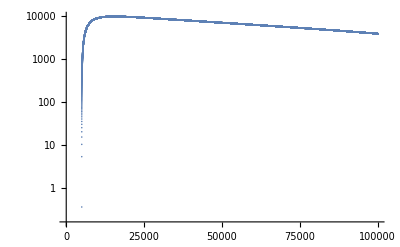

```mathematica
ListLogPlot[psivac]
```

### Fisher

We then use the Fisher and covariance matrix solver of Maselli to solve for the uncertainties in density. This is for a 4-year LISA mission. Its input parameters are (in order): the dimensions of the n x n Fisher matrix (that depends on the number of parameters to be included, which is 6 in our case), the distance of the binary (in Mpc), masses of the binary, effective spin, index of the environmental effect, and PSD. In our case, we only use LISA. This function calculates the frequency range for LISA, the SNR of the vacuum waveform, the number of orbit cycles the binary completes in the same frequency range as the SNR, and the Fisher and covariance matrix elements.

```mathematica
Fisher[dim_,𝒹_,m1_,m2_,χeff_,index_,PSD_]:=Block[{ℳ,η,q=m1/m2,d,τ,ϕ,χ, ρ0,𝒽,d𝒽,
	ρ,C,𝒫,i,j,Γ,Σ,Noise,fmin,fmax,f,IscoS,𝒯=4,𝒩,amp},

Off[NIntegrate::slwcon];
Off[NIntegrate::eincr];

Which[PSD == "zerodet", Noise = zerodet, PSD == "ET", Noise = ET,PSD == "LISA", 
	Noise = LISA,PSD == "CE", Noise = CE,PSD == "DECIGO", Noise = DECIGO];

C=If[PSD == "LISA",Sqrt[5],1];

(* ---- Creating the vacuum waveform from the input parameters ---- *)
(* ---- Binary parameters q = m1/m2 ≥ 1 ---- *)
{ℳ,η,τ,ϕ,χ,d} = {(q/(1+q)^2)^(3/5)msun (m1+m2),q/(1+q)^2,0,-π/4,χeff,𝒹};
 
(* ---- environmental correction ---- *)

ρ0  = 0;

IscoS=cc 𝒻1[(m1+m2)msun,η,χ]+0cc/(π 6^(3/2)(m1+m2)msun); (* PhenomB I-M transition freq *)
amp[f_]=C (2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6); (* Constant amplitude, based only on Subscript[d, L] and chirp mass *)
𝒽[f_] =amp[f] hPhBppE[f/cc][ℳ,η,χ,τ,ϕ,d,ρ0,index];
(*d𝒽[f_] = amp[f]Table[deriv[[i]][f],{i,1,dim}]; *)

d𝒽[f_] = amp[f]dhdθ[f/cc,index]; (* differentiated waveform; input for Fisher integral *)

Print["𝒞 = ",C," -- ℳ/M_⊙, = ",ℳ/msun,"-- η = ",N[η]," -- χ_eff = ",χ];

(* ---- Setting the limits of integration per detector ---- *)
Which[PSD == "zerodet", fmin = 10,
	PSD == "LISA", fmin = Max[10^-5,4.149 10^-5 (ℳ/msun 10^-6)^(-5/8) 𝒯^(-3/8)], 
	PSD == "ET", fmin = 3, 
	PSD == "CE", fmin = 5,
	PSD == "DECIGO", fmin = 0.01];

Which[PSD == "zerodet", fmax = IscoS, 
	PSD == "LISA",fmax = Min[1,IscoS],
	PSD == "ET", fmax = IscoS, 
	PSD == "CE", fmax = IscoS,
	PSD == "DECIGO", fmax = Min[100,IscoS]];

(* ---- Signal to noise ratio ---- *)

ρ = Sqrt[𝒪[Noise[f],𝒽[f],𝒽[f],fmin,fmax]];
𝒩 = NIntegrate[f/cc^2/(96/(5π ℳ^2) (π ℳ f/cc)^(11/3)),{f,fmin,fmax}];

Print["PSD = ",PSD," -- [\!\(\*SubscriptBox[\(f\), \(min\)]\),\!\(\*SubscriptBox[\(f\), \(max\)]\)] = [",fmin," , ",fmax,"]Hz -- ρ = ",NumberForm[ρ,6]," -- # cycles = ",𝒩];

(* ---- This a prior on the spin parameters |Subscript[χ, 1,2]|≤1 ---- *)

Γ = ConstantArray[0,{dim,dim}];

(* ---- Compute the Fisher and Covariance Matrix ---- *)

Monitor[For[i=1,i<=dim,i++,
	For[j=1,j<=i,j++,
		Γ[[i,j]] = If[i==j,𝒪[Noise[f],d𝒽[f][[i]],d𝒽[f][[j]],fmin,fmax],
								2𝒪[Noise[f],d𝒽[f][[i]],d𝒽[f][[j]],fmin,fmax]];
		]
	],
	Γ//MatrixForm];

Γ = Normal[Symmetrize[Γ]];

Print["Positive Matrix ? "PositiveDefiniteMatrixQ[Γ]];

Σ=If[PositiveDefiniteMatrixQ[Γ],LinearSolve[Γ,IdentityMatrix[dim],Method->"Cholesky"],Inverse[Γ]];

Return[{Γ,Σ}];

]
```

We then solve for the uncertainties in the surrounding density σ_ρ_0, divided by water density 10^3 kg/m^3 using `errI` and `errI2`.

```mathematica
Assuming[M∈Reals&&ℳ∈Reals &&γ∈Reals&&𝓀0∈Reals&&γ>0&&M>0&&ℳ>0&&𝓀0>0,FullSimplify[Sqrt[D[ρ0phys,M]^2 σM^2+D[ρ0phys,Mc]^2 σMc^2+D[ρ0phys,η]^2 ση^2+D[ρ0phys,ρ0B]^2 σρ0^2//.ρ0B->0]]]
```

(M^(-2+γ) π^-γ ℳ^-γ √(σρ0^2))/𝓀0

```mathematica
errI[m1_,m2_,γ_,matrix_]:=With[{cc=2.998*10^8,G=6.67408 10^-11,M=(m1+m2)1.4768,Mc=(m1 m2)^(3/5)/(m1+m2)^(1/5)1.4768,ρH20=10^3},cc^2/G(Mc π)^-γ/(10^6 M^(2-γ))(Sqrt[Diagonal[matrix[[1,2]]]][[-1]])/ρH20]

errI2[m1_,m2_,γ_,matrix_,k0_]:=With[{cc=2.998*10^8,G=6.67408 10^-11,M=(m1+m2)1.4768,Mc=(m1 m2)^(3/5)/(m1+m2)^(1/5)1.4768,ρH20=10^3},cc^2/G(Mc π)^-γ/(10^6 M^(2-γ))(Sqrt[Diagonal[matrix[[1,2]]]][[-1]])/(ρH20 Abs[k0[m1,m2]])]
```

### Sample runs

```mathematica
{m1,m2,χ1,χ2}={10^5,10,0.8,0.5}; (* q=10^4 *)
χefftry=(χ1 m1+χ2 m2)/(m1+m2);
```

```mathematica
Fisherpulltry=Fisher[6,1000,m1,m2,χefftry,-2,"RobsonLISA"];
```

𝒞 = √5 -- ℳ/M_⊙, = 398.099-- η = 0.00009998 -- χ_eff = 0.79997

PSD = RobsonLISA -- [f_min,f_max] = [0.00328985 , 0.113325]Hz -- ρ = 61.0029 -- # cycles = 658378.

Positive Matrix ?  True

```mathematica
Export["try.h5",Fisherpulltry];
```

```mathematica
datatry=Import["try.h5","Data"];
errI[10^5,10,2,datatry]
```

0.000185107

```mathematica
{m1,m2,χ1,χ2}={10^7,10,0.8,0.5}; (* q=10^6 *)
χefftry=(χ1 m1+χ2 m2)/(m1+m2);
Fisherpulltry=Fisher[6,1000,m1,m2,χefftry,-2,"LISA"];
```

### The next runs comprise of the full calculation used in the plots to be included, divided into I/EMRI and the different effects. We see that the calculations fail for m_1=10^7and above since the binary is already at the ISCO 4 years before the merger (f_min> f_max). Also, Ajith et. al’s IMRPhenomB is not really calibrated for high mass ratios, so it would be better to use more accurate frequency domain waveforms specially built for LISA.

IMRI -- Grav pull

```mathematica
Monitor[With[{m2=10,χ1=0.8,χ2=0.5},For[i=2,i<5,i++,m1=10^i;
χeffIMRI=(χ1 m1+χ2 m2)/(m1+m2);FisherIMRI=Fisher[6,1000,m1,m2,χeffIMRI,-2,"LISA"];Do[Export["IMRIFisherlogm1"<>ToString[i]<>".h5",FisherIMRI],i]]],m1]
```

𝒞 = √5 -- ℳ/M_⊙, = 24.6446-- η = 0.0826446 -- χ_eff = 0.772727

PSD = LISA -- [f_min,f_max] = [0.0187217 , 1]Hz -- ρ = 1.50392 -- # cycles = 3.752×10^6

Positive Matrix ?  True

𝒞 = √5 -- ℳ/M_⊙, = 62.9703-- η = 0.00980296 -- χ_eff = 0.79703

PSD = LISA -- [f_min,f_max] = [0.0104162 , 1]Hz -- ρ = 6.20650 -- # cycles = 2.08923×10^6

Positive Matrix ?  True

𝒞 = √5 -- ℳ/M_⊙, = 158.458-- η = 0.000998003 -- χ_eff = 0.7997

PSD = LISA -- [f_min,f_max] = [0.00585093 , 1]Hz -- ρ = 21.9370 -- # cycles = 1.17391×10^6

Positive Matrix ?  True

IMRI -- Grav drag

```mathematica
Monitor[With[{m2=10,χ1=0.8,χ2=0.5},For[i=2,i<5,i++,m1=10^i;
χeffIMRI=(χ1 m1+χ2 m2)/(m1+m2);FisherIMRI=Fisher[6,1000,m1,m2,χeffIMRI,-11/3,"LISA"];Do[Export["IMRIFisherdraglogm1"<>ToString[i]<>".h5",FisherIMRI],i]]],m1]
```

𝒞 = √5 -- ℳ/M_⊙, = 24.6446-- η = 0.0826446 -- χ_eff = 0.772727

PSD = LISA -- [f_min,f_max] = [0.0187217 , 1]Hz -- ρ = 1.50392 -- # cycles = 3.752×10^6

Positive Matrix ?  True

𝒞 = √5 -- ℳ/M_⊙, = 62.9703-- η = 0.00980296 -- χ_eff = 0.79703

PSD = LISA -- [f_min,f_max] = [0.0104162 , 1]Hz -- ρ = 6.20650 -- # cycles = 2.08923×10^6

Positive Matrix ?  True

𝒞 = √5 -- ℳ/M_⊙, = 158.458-- η = 0.000998003 -- χ_eff = 0.7997

PSD = LISA -- [f_min,f_max] = [0.00585093 , 1]Hz -- ρ = 21.9370 -- # cycles = 1.17391×10^6

Positive Matrix ?  True

IMRI -- Collisionless accretion

```mathematica
Monitor[With[{m2=10,χ1=0.8,χ2=0.5},For[i=2,i<5,i++,m1=10^i;
χeffIMRI=(χ1 m1+χ2 m2)/(m1+m2);FisherIMRI=Fisher[6,1000,m1,m2,χeffIMRI,-3,"LISA"];Do[Export["IMRIFishercollesslogm1"<>ToString[i]<>".h5",FisherIMRI],i]]],m1]
```

𝒞 = √5 -- ℳ/M_⊙, = 24.6446-- η = 0.0826446 -- χ_eff = 0.772727

PSD = LISA -- [f_min,f_max] = [0.0187217 , 1]Hz -- ρ = 1.50392 -- # cycles = 3.752×10^6

Positive Matrix ?  True

𝒞 = √5 -- ℳ/M_⊙, = 62.9703-- η = 0.00980296 -- χ_eff = 0.79703

PSD = LISA -- [f_min,f_max] = [0.0104162 , 1]Hz -- ρ = 6.20650 -- # cycles = 2.08923×10^6

Positive Matrix ?  True

𝒞 = √5 -- ℳ/M_⊙, = 158.458-- η = 0.000998003 -- χ_eff = 0.7997

PSD = LISA -- [f_min,f_max] = [0.00585093 , 1]Hz -- ρ = 21.9370 -- # cycles = 1.17391×10^6

Positive Matrix ?  True

EMRI - Grav pull

```mathematica
Monitor[With[{m2=10,χ1=0.8,χ2=0.5},For[i=5,i<10,i++,m1=10^i;
χeffEMRI=(χ1 m1+χ2 m2)/(m1+m2);FisherEMRI=Fisher[6,1000,m1,m2,χeffEMRI,-2,"LISA"];Do[Export["EMRIFisherpulllogm1"<>ToString[i]<>".h5",FisherEMRI],i]]],m1]
```

𝒞 = √5 -- ℳ/M_⊙, = 398.099-- η = 0.00009998 -- χ_eff = 0.79997

PSD = LISA -- [f_min,f_max] = [0.00328985 , 0.113325]Hz -- ρ = 64.3190 -- # cycles = 658378.

Positive Matrix ?  True

𝒞 = √5 -- ℳ/M_⊙, = 999.998-- η = 9.9998×10^-6 -- χ_eff = 0.799997

PSD = LISA -- [f_min,f_max] = [0.00185 , 0.0113276]Hz -- ρ = 142.360 -- # cycles = 353132.

Positive Matrix ?  True

𝒞 = √5 -- ℳ/M_⊙, = 2511.89-- η = 9.99998×10^-7 -- χ_eff = 0.8

PSD = LISA -- [f_min,f_max] = [0.00104033 , 0.00113271]Hz -- ρ = 17.2351 -- # cycles = 27598.8

Positive Matrix ?  True

𝒞 = √5 -- ℳ/M_⊙, = 6309.57-- η = 1.×10^-7 -- χ_eff = 0.8

PSD = LISA -- [f_min,f_max] = [0.00058502 , 0.000113271]Hz -- ρ = 22.5346 ⅈ -- # cycles = -1.6943×10^6

Positive Matrix ?  False

Inverse::luc: Result for Inverse of badly conditioned matrix {{-1.63094739234850975910262126517×10^15,-3.03342001552515795438116972108×10^15,-9.01514492090887799533284790486,-9.01307104858726614087354585196×10^8,9.14183873696292303404113876998×10^15,-2.09430239341844297225370475851×10^23},«4»,{-2.09430239341844297225370475851×10^23,-8.79686710410743532515764959038×10^23,-1.343083083729273854234216763×10^9,-1.9777137955988855415648433729×10^17,1.84644897798308722926079502344×10^24,-7.56302595696744194339856656086×10^32}} may contain significant numerical errors.

𝒞 = √5 -- ℳ/M_⊙, = 15848.9-- η = 1.×10^-8 -- χ_eff = 0.8

PSD = LISA -- [f_min,f_max] = [0.000328981 , 0.000011327]Hz -- ρ = 14.7635 ⅈ -- # cycles = -1.8051×10^7

Positive Matrix ?  False

Inverse::luc: Result for Inverse of badly conditioned matrix {{-2.34914933214643725978490133135×10^16,-2.92341826910304847684327151557×10^16,-12.3670799986751557623954729706,-2.24782135578574896786255594654×10^9,1.90264826371774747863102630721×10^17,-3.27171918352412748423582695716×10^23},«4»,{-3.27171918352412748423582695716×10^23,-4.83164109396779375841171438386×10^23,-8.78782002406267214357879067312×10^7,-2.47940190934996011426357611984×10^16,2.27242443741247157521474580022×10^24,-4.14327107428559977656181559642×10^32}} may contain significant numerical errors.

EMRI -- Grav drag

```mathematica
Monitor[With[{m2=10,χ1=0.8,χ2=0.5},For[i=5,i<10,i++,m1=10^i;
χeffEMRI=(χ1 m1+χ2 m2)/(m1+m2);FisherEMRI=Fisher[6,1000,m1,m2,χeffEMRI,-11/3,"LISA"];Do[Export["EMRIFisherdraglogm1"<>ToString[i]<>".h5",FisherEMRI],i]]],m1]
```

𝒞 = √5 -- ℳ/M_⊙, = 398.099-- η = 0.00009998 -- χ_eff = 0.79997

PSD = LISA -- [f_min,f_max] = [0.00328985 , 0.113325]Hz -- ρ = 64.3190 -- # cycles = 658378.

Positive Matrix ?  True

𝒞 = √5 -- ℳ/M_⊙, = 999.998-- η = 9.9998×10^-6 -- χ_eff = 0.799997

PSD = LISA -- [f_min,f_max] = [0.00185 , 0.0113276]Hz -- ρ = 142.360 -- # cycles = 353132.

Positive Matrix ?  True

𝒞 = √5 -- ℳ/M_⊙, = 2511.89-- η = 9.99998×10^-7 -- χ_eff = 0.8

PSD = LISA -- [f_min,f_max] = [0.00104033 , 0.00113271]Hz -- ρ = 17.2351 -- # cycles = 27598.8

Positive Matrix ?  True

𝒞 = √5 -- ℳ/M_⊙, = 6309.57-- η = 1.×10^-7 -- χ_eff = 0.8

PSD = LISA -- [f_min,f_max] = [0.00058502 , 0.000113271]Hz -- ρ = 22.5346 ⅈ -- # cycles = -1.6943×10^6

Positive Matrix ?  False

Inverse::luc: Result for Inverse of badly conditioned matrix {{-1.63094739234850975910262126517×10^15,-3.03342001552515795438116972108×10^15,-9.01514492090887799533284790486,-9.01307104858726614087354585196×10^8,9.14183873696292303404113876998×10^15,-1.07977606159066550066711340316×10^30},«4»,{-1.07977606159066550066711340316×10^30,-5.22738378977414767227123741156×10^31,-4.73471360041993007904580604155×10^16,-9.79326363489531053567566082796×10^24,8.25765198589346041364867289229×10^31,-1.16745557653127816497984158319×10^49}} may contain significant numerical errors.

𝒞 = √5 -- ℳ/M_⊙, = 15848.9-- η = 1.×10^-8 -- χ_eff = 0.8

PSD = LISA -- [f_min,f_max] = [0.000328981 , 0.000011327]Hz -- ρ = 14.7635 ⅈ -- # cycles = -1.8051×10^7

Positive Matrix ?  False

Inverse::luc: Result for Inverse of badly conditioned matrix {{-2.34914933214643725978490133135×10^16,-2.92341826910304847684327151557×10^16,-12.3670799986751557623954729706,-2.24782135578574896786255594654×10^9,1.90264826371774747863102630721×10^17,-2.14784236701695764534273159361×10^31},{-«64»,-«64»,-«64»,-«56»,«65»,-«60»},«2»,{«1»},{-2.14784236701695764534273159361×10^31,-4.79340881277355784890952302427×10^31,-2.23271773807379414918987273934×10^15,-«53»,1.40024043726769510568596081293×10^32,-1.38834761261194298134575737775×10^50}} may contain significant numerical errors.

EMRI -- Collisionless Accretion

```mathematica
Monitor[With[{m2=10,χ1=0.8,χ2=0.5},For[i=5,i<10,i++,m1=10^i;
χeffEMRI=(χ1 m1+χ2 m2)/(m1+m2);FisherEMRI=Fisher[6,1000,m1,m2,χeffEMRI,-3,"LISA"];Do[Export["EMRIFishercollesslogm1"<>ToString[i]<>".h5",FisherEMRI],i]]],m1]
```

𝒞 = √5 -- ℳ/M_⊙, = 398.099-- η = 0.00009998 -- χ_eff = 0.79997

PSD = LISA -- [f_min,f_max] = [0.00328985 , 0.113325]Hz -- ρ = 64.3190 -- # cycles = 658378.

Positive Matrix ?  True

𝒞 = √5 -- ℳ/M_⊙, = 999.998-- η = 9.9998×10^-6 -- χ_eff = 0.799997

PSD = LISA -- [f_min,f_max] = [0.00185 , 0.0113276]Hz -- ρ = 142.360 -- # cycles = 353132.

Positive Matrix ?  True

𝒞 = √5 -- ℳ/M_⊙, = 2511.89-- η = 9.99998×10^-7 -- χ_eff = 0.8

PSD = LISA -- [f_min,f_max] = [0.00104033 , 0.00113271]Hz -- ρ = 17.2351 -- # cycles = 27598.8

Positive Matrix ?  True

𝒞 = √5 -- ℳ/M_⊙, = 6309.57-- η = 1.×10^-7 -- χ_eff = 0.8

PSD = LISA -- [f_min,f_max] = [0.00058502 , 0.000113271]Hz -- ρ = 22.5346 ⅈ -- # cycles = -1.6943×10^6

Positive Matrix ?  False

Inverse::luc: Result for Inverse of badly conditioned matrix {{-1.63094739234850975910262126517×10^15,-3.03342001552515795438116972108×10^15,-9.01514492090887799533284790486,-9.01307104858726614087354585196×10^8,9.14183873696292303404113876998×10^15,-3.95316137453273283281686547723×10^27},«4»,{-3.95316137453273283281686547723×10^27,-3.80413226245161365627314390499×10^28,-4.24494202866445867601941126992×10^13,-7.63273043563922305311037989042×10^21,6.72597364549694322349924224757×10^28,-3.67194882543454529202553758531×10^42}} may contain significant numerical errors.

𝒞 = √5 -- ℳ/M_⊙, = 15848.9-- η = 1.×10^-8 -- χ_eff = 0.8

PSD = LISA -- [f_min,f_max] = [0.000328981 , 0.000011327]Hz -- ρ = 14.7635 ⅈ -- # cycles = -1.8051×10^7

Positive Matrix ?  False

Inverse::luc: Result for Inverse of badly conditioned matrix {{-2.34914933214643725978490133135×10^16,-2.92341826910304847684327151557×10^16,-12.3670799986751557623954729706,-2.24782135578574896786255594654×10^9,1.90264826371774747863102630721×10^17,-1.36273325581228135183726006022×10^28},«4»,{-1.36273325581228135183726006022×10^28,-2.51744127667825524434249701316×10^28,-2.11863061721518642985959519161×10^12,-9.32119957114650089524482299778×10^20,8.88868234317306646877145523719×10^28,-1.17143406048364143471871294557×10^43}} may contain significant numerical errors.

A manual loop was then used for calculating the individual values of the uncertainties for all runs.

```mathematica
datapullq10e1=Import["IMRIFisherlogm12.h5","Data"];
datapullq10e2=Import["IMRIFisherlogm13.h5","Data"];
datapullq10e3=Import["IMRIFisherlogm14.h5","Data"];
datapullq10e4=Import["EMRIFisherpulllogm15.h5","Data"];
datapullq10e5=Import["EMRIFisherpulllogm16.h5","Data"];
datapullq10e6=Import["EMRIFisherpulllogm17.h5","Data"];
datapullq10e7=Import["EMRIFisherpulllogm18.h5","Data"];
datapullq10e8=Import["EMRIFisherpulllogm19.h5","Data"];
```

```mathematica
Table[With[{cc=2.998*10^8,G=6.67408 10^-11,M=(10^5+10)1.4768,Mc=((10^6)^(3/5))/((10^5+10)^(1/5))1.4768},cc^2/G(Mc π)^-2/(10^6 M^(2-2))Sqrt[Diagonal[datapullq10e4[[1,2]]]][[d]]],{d,1,6}]
```

{1.87585×10^9,1.17474×10^11,3.83801×10^20,1.44018×10^15,2.01821×10^10,0.177865}

```mathematica
datadragq10e1=Import["IMRIFisherdraglogm12.h5","Data"];
datadragq10e2=Import["IMRIFisherdraglogm13.h5","Data"];
datadragq10e3=Import["IMRIFisherdraglogm14.h5","Data"];
datadragq10e4=Import["EMRIFisherdraglogm15.h5","Data"];
datadragq10e5=Import["EMRIFisherdraglogm16.h5","Data"];
datadragq10e6=Import["EMRIFisherdraglogm17.h5","Data"];
datadragq10e7=Import["EMRIFisherdraglogm18.h5","Data"];
datadragq10e8=Import["EMRIFisherdraglogm19.h5","Data"];
```

```mathematica
datacollessq10e1=Import["IMRIFishercollesslogm12.h5","Data"];
datacollessq10e2=Import["IMRIFishercollesslogm13.h5","Data"];
datacollessq10e3=Import["IMRIFishercollesslogm14.h5","Data"];
datacollessq10e4=Import["EMRIFishercollesslogm15.h5","Data"];
datacollessq10e5=Import["EMRIFishercollesslogm16.h5","Data"];
datacollessq10e6=Import["EMRIFishercollesslogm17.h5","Data"];
datacollessq10e7=Import["EMRIFishercollesslogm18.h5","Data"];
datacollessq10e8=Import["EMRIFishercollesslogm19.h5","Data"];
```

```mathematica
sigmarho0q10e1pull=errI[10^2,10,2,datapullq10e1]
sigmarho0q10e2pull=errI[10^3,10,2,datapullq10e2]
sigmarho0q10e3pull=errI[10^4,10,2,datapullq10e3]
sigmarho0q10e4pull=errI[10^5,10,2,datapullq10e4]
sigmarho0q10e5pull=errI[10^6,10,2,datapullq10e5]
sigmarho0q10e6pull=errI[10^7,10,2,datapullq10e6]
sigmarho0q10e7pull=errI[10^8,10,2,datapullq10e7]
sigmarho0q10e8pull=errI[10^9,10,2,datapullq10e8]
```

0.0628874

0.00548479

0.000910462

0.000177865

0.000146644

2.28289

0.+2.23157×10^-6 ⅈ

0.+4.60109×10^-8 ⅈ

```mathematica
logm1=Table[i,{i,2,9}]
```

{2,3,4,5,6,7,8,9}

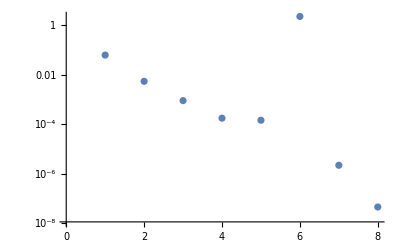

```mathematica
ListLogPlot[{sigmarho0q10e1pull,sigmarho0q10e2pull,sigmarho0q10e3pull,sigmarho0q10e4pull,sigmarho0q10e5pull,sigmarho0q10e6pull,Im[sigmarho0q10e7pull],Im[sigmarho0q10e8pull]}]
```

5.04704×10^-12

9.7669×10^-15

2.91398×10^-17

1.06307×10^-19

1.3027×10^-21

2.00028×10^-19

0.+4.58518×10^-28 ⅈ

0.+3.27618×10^-32 ⅈ

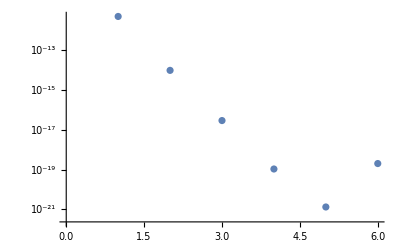

```mathematica
sigmarho0q10e1drag=errI2[10^2,10,11/3,datadragq10e1,kβdrag]
sigmarho0q10e2drag=errI2[10^3,10,11/3,datadragq10e2,kβdrag]
sigmarho0q10e3drag=errI2[10^4,10,11/3,datadragq10e3,kβdrag]
sigmarho0q10e4drag=errI2[10^5,10,11/3,datadragq10e4,kβdrag]
sigmarho0q10e5drag=errI2[10^6,10,11/3,datadragq10e5,kβdrag]
sigmarho0q10e6drag=errI2[10^7,10,11/3,datadragq10e6,kβdrag]
sigmarho0q10e7drag=errI2[10^8,10,11/3,datadragq10e7,kβdrag]
sigmarho0q10e8drag=errI2[10^9,10,11/3,datadragq10e8,kβdrag]
ListLogPlot[{sigmarho0q10e1drag,sigmarho0q10e2drag,sigmarho0q10e3drag,sigmarho0q10e4drag,sigmarho0q10e5drag,sigmarho0q10e6drag,sigmarho0q10e7drag,sigmarho0q10e8drag}]
```

```mathematica
sigmarho0q10e1colless=errI2[10^2,10,3,datacollessq10e1,kβaccretion]
sigmarho0q10e2colless=errI2[10^3,10,3,datacollessq10e2,kβaccretion]
sigmarho0q10e3colless=errI2[10^4,10,3,datacollessq10e3,kβaccretion]
sigmarho0q10e4colless=errI2[10^5,10,3,datacollessq10e4,kβaccretion]
sigmarho0q10e5colless=errI2[10^6,10,3,datacollessq10e5,kβaccretion]
sigmarho0q10e6colless=errI2[10^7,10,3,datacollessq10e6,kβaccretion]
sigmarho0q10e7colless=errI2[10^8,10,3,datacollessq10e7,kβaccretion]
sigmarho0q10e8colless=errI2[10^9,10,3,datacollessq10e8,kβaccretion]
```

7.76716×10^-7

4.45914×10^-8

4.19096×10^-9

4.75143×10^-10

1.95779×10^-10

1.20679×10^-6

0.+1.96971×10^-13 ⅈ

0.+9.04775×10^-16 ⅈ

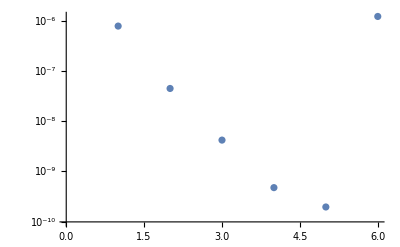

```mathematica
ListLogPlot[{sigmarho0q10e1colless,sigmarho0q10e2colless,sigmarho0q10e3colless,sigmarho0q10e4colless,sigmarho0q10e5colless,sigmarho0q10e6colless,sigmarho0q10e7colless,sigmarho0q10e8colless}]
```

We then collect the values for m_1=10^2-10^6 M_sunand plot them together with the best fit line for the equation log σ_ρ_0= a log m_1+ b, where a is the slope and b is the y-intercept.

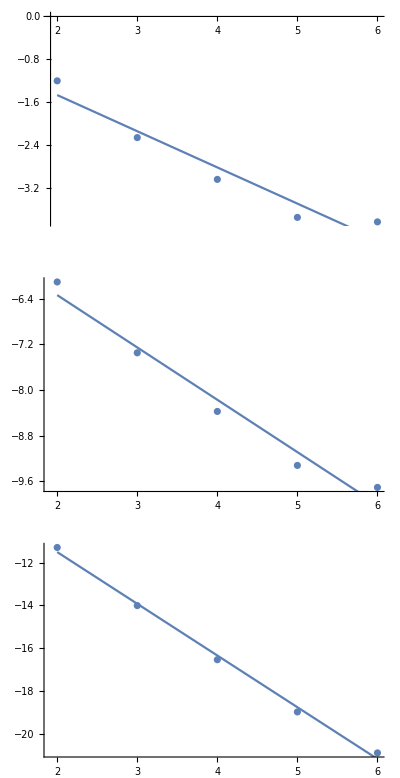
```mathematica
6/16/21 11:15:40 In[93]:= 
sigmarho0pull = {0.0628874, 0.00548479, 0.000910462, 0.000177865, 
   0.000146644};
sigmarho0drag = {0.00000000000504704, 0.0000000000000097669, 
   2.91398*10^-17, 1.06307*10^-19, 1.3027*10^-21};
sigmarho0colless = {0.000000776716, 0.0000000445914, 0.00000000419096,
    0.000000000475143, 0.000000000195779};
m1list = {10^2, 10^3, 10^4, 10^5, 10^6}

6/16/21 11:15:40 Out[96]= {100, 1000, 10000, 100000, 1000000}

6/16/21 11:20:36 In[103]:= logsigmapulltable = 
 Join[Transpose[{Log10[m1list]}], Transpose[{Log10[sigmarho0pull]}], 
  2]; logsigmadragtable = 
 Join[Transpose[{Log10[m1list]}], Transpose[{Log10[sigmarho0drag]}], 
  2]; logsigmacollesstable = 
 Join[Transpose[{Log10[m1list]}], 
  Transpose[{Log10[sigmarho0colless]}], 2];

6/16/21 11:23:58 In[104]:= pullbestfit[x_] := -0.6754 x - 0.1159;
dragbestfit[x_] := -2.414 x - 6.684;
collessbestfit[x_] := -0.9169 x - 4.506;

6/16/21 11:28:53 In[112]:= GraphicsColumn[{Show[
   ListPlot[logsigmapulltable], 
   Plot[pullbestfit[x], {x, 2, 6}, PlotRange -> Full]], 
  Show[ListPlot[logsigmacollesstable], 
   Plot[collessbestfit[x], {x, 2, 6}, PlotRange -> Full]], 
  Show[ListPlot[logsigmadragtable], 
   Plot[dragbestfit[x], {x, 2, 6}, PlotRange -> Full]]}, Frame -> True]

6/16/21 11:28:54 Out[112]= -Graphics-
```

(It’s easier to plot using matplotlib for me)

### PCA

Here we expound further on the data we got from the Fisher analysis. We can immediately compute the principal components by “getting the eigendecomposition of the covariance matrix” (from Wiki).

```mathematica
datapullq10e1=Import["IMRIFisherlogm12.h5","Data"];
datapullq10e2=Import["IMRIFisherlogm13.h5","Data"];
datapullq10e3=Import["IMRIFisherlogm14.h5","Data"];
datapullq10e4=Import["EMRIFisherpulllogm15.h5","Data"];
datapullq10e5=Import["EMRIFisherpulllogm16.h5","Data"];
datapullq10e6=Import["EMRIFisherpulllogm17.h5","Data"];
datapullq10e7=Import["EMRIFisherpulllogm18.h5","Data"];
datapullq10e8=Import["EMRIFisherpulllogm19.h5","Data"];
datadragq10e1=Import["IMRIFisherdraglogm12.h5","Data"];
datadragq10e2=Import["IMRIFisherdraglogm13.h5","Data"];
datadragq10e3=Import["IMRIFisherdraglogm14.h5","Data"];
datadragq10e4=Import["EMRIFisherdraglogm15.h5","Data"];
datadragq10e5=Import["EMRIFisherdraglogm16.h5","Data"];
datadragq10e6=Import["EMRIFisherdraglogm17.h5","Data"];
datadragq10e7=Import["EMRIFisherdraglogm18.h5","Data"];
datadragq10e8=Import["EMRIFisherdraglogm19.h5","Data"];
datacollessq10e1=Import["IMRIFishercollesslogm12.h5","Data"];
datacollessq10e2=Import["IMRIFishercollesslogm13.h5","Data"];
datacollessq10e3=Import["IMRIFishercollesslogm14.h5","Data"];
datacollessq10e4=Import["EMRIFishercollesslogm15.h5","Data"];
datacollessq10e5=Import["EMRIFishercollesslogm16.h5","Data"];
datacollessq10e6=Import["EMRIFishercollesslogm17.h5","Data"];
datacollessq10e7=Import["EMRIFishercollesslogm18.h5","Data"];
datacollessq10e8=Import["EMRIFishercollesslogm19.h5","Data"];
```

Recall the form of the data we have: a 6x6x2 matrix, for which the first z component consisting of a 6x6 matrix is the Fisher matrix and the 2nd is its corresponding 6x6 covariance matrix. In the covariance matrix, we have the diagonals as the variance with respect to the following: ln chirp mass, ln symmetric mass ratio, coalescence time, coalescence phase, effective spin, and environmental density.

```mathematica
datapullq10e4[[1]]//MatrixForm
```

((6.87237×10^15
-6.086×10^13
-503.272
-4.46366×10^9
-6.36932×10^14
-6.02103×10^24) | (-6.086×10^13
9.65004×10^11
10.9283
6.22338×10^7
6.75163×10^12
3.90467×10^22) | (-503.272
10.9283
2.02814×10^-10
0.000712699
61.202
2.95833×10^11) | (-4.46366×10^9
6.22338×10^7
0.000712699
4136.93
4.71145×10^8
3.21115×10^18) | (-6.36932×10^14
6.75163×10^12
61.202
4.71145×10^8
6.20573×10^13
5.15539×10^23) | (-6.02103×10^24
3.90467×10^22
2.95833×10^11
3.21115×10^18
5.15539×10^23
6.0144×10^33)
(2.2579×10^-11
-1.40174×10^-9
-4.09627
0.0000168898
2.4284×10^-10
2.07251×10^-21) | (-1.40174×10^-9
8.855×10^-8
269.675
-0.00108017
-1.50511×10^-8
-1.24574×10^-19) | (-4.09627
269.675
9.45193×10^11
-3.41023×10^6
-43.596
-3.40367×10^-10) | (0.0000168898
-0.00108017
-3.41023×10^6
13.3088
0.000180975
1.47037×10^-15) | (2.4284×10^-10
-1.50511×10^-8
-43.596
0.000180975
2.61361×10^-9
2.23108×10^-20) | (2.07251×10^-21
-1.24574×10^-19
-3.40367×10^-10
1.47037×10^-15
2.23108×10^-20
2.02997×10^-31))

We then get the eigenvalues of the corresponding covariance matrix.

```mathematica
Eigenvectors[datapullq10e4[[1,2]]]//MatrixForm
Eigenvalues[datapullq10e4[[1,2]]]//MatrixForm
```

(-4.33379×10^-12 | 2.85312×10^-10 | 1. | -3.60797×10^-6 | -4.61239×10^-11 | 0.
-2.46525×10^-6 | 0.000113325 | -3.60797×10^-6 | -1. | -0.0000272825 | 0.
0.0236789 | -0.486631 | -1.45547×10^-11 | -0.0000313804 | -0.873287 | 0.
-0.0478636 | 0.871978 | 1.33447×10^-10 | 0.000112227 | -0.487199 | 0.
0.998573 | 0.053335 | 2.17421×10^-12 | 3.65461×10^-6 | -0.00264445 | 0.
0. | 0. | 0. | 0. | 0. | 1.)

(9.45193×10^11
1.0048
-1.26529×10^-9
1.78757×10^-10
3.61858×10^-14
5.7752×10^-34)

```mathematica
{PCAvalspullq10e1,PCAvecspullq10e1}=Eigensystem[datapullq10e1[[1,2]]];
{PCAvalspullq10e2,PCAvecspullq10e2}=Eigensystem[datapullq10e2[[1,2]]];
{PCAvalspullq10e3,PCAvecspullq10e3}=Eigensystem[datapullq10e3[[1,2]]];
{PCAvalspullq10e4,PCAvecspullq10e4}=Eigensystem[datapullq10e4[[1,2]]];
{PCAvalspullq10e5,PCAvecspullq10e5}=Eigensystem[datapullq10e5[[1,2]]];
{PCAvalspullq10e6,PCAvecspullq10e6}=Eigensystem[datapullq10e6[[1,2]]];
{PCAvalspullq10e7,PCAvecspullq10e7}=Eigensystem[datapullq10e7[[1,2]]];
{PCAvalspullq10e8,PCAvecspullq10e8}=Eigensystem[datapullq10e8[[1,2]]];
{PCAvalsdragq10e1,PCAvecsdragq10e1}=Eigensystem[datadragq10e1[[1,2]]];
{PCAvalsdragq10e2,PCAvecsdragq10e2}=Eigensystem[datadragq10e2[[1,2]]];
{PCAvalsdragq10e3,PCAvecsdragq10e3}=Eigensystem[datadragq10e3[[1,2]]];
{PCAvalsdragq10e4,PCAvecsdragq10e4}=Eigensystem[datadragq10e4[[1,2]]];
{PCAvalsdragq10e5,PCAvecsdragq10e5}=Eigensystem[datadragq10e5[[1,2]]];
{PCAvalsdragq10e6,PCAvecsdragq10e6}=Eigensystem[datadragq10e6[[1,2]]];
{PCAvalsdragq10e7,PCAvecsdragq10e7}=Eigensystem[datadragq10e7[[1,2]]];
{PCAvalsdragq10e8,PCAvecsdragq10e8}=Eigensystem[datadragq10e8[[1,2]]];
{PCAvalscollessq10e1,PCAvecscollessq10e1}=Eigensystem[datacollessq10e1[[1,2]]];
{PCAvalscollessq10e2,PCAvecscollessq10e2}=Eigensystem[datacollessq10e2[[1,2]]];
{PCAvalscollessq10e3,PCAvecscollessq10e3}=Eigensystem[datacollessq10e3[[1,2]]];
{PCAvalscollessq10e4,PCAvecscollessq10e4}=Eigensystem[datacollessq10e4[[1,2]]];
{PCAvalscollessq10e5,PCAvecscollessq10e5}=Eigensystem[datacollessq10e5[[1,2]]];
{PCAvalscollessq10e6,PCAvecscollessq10e6}=Eigensystem[datacollessq10e6[[1,2]]];
{PCAvalscollessq10e7,PCAvecscollessq10e7}=Eigensystem[datacollessq10e7[[1,2]]];
{PCAvalscollessq10e8,PCAvecscollessq10e8}=Eigensystem[datacollessq10e8[[1,2]]];
```

```mathematica
PCAvalspullq10e4
PCAvecspullq10e4//MatrixForm
```

{9.45193×10^11,1.00513,-9.93234×10^-10,-3.49425×10^-11,4.06991×10^-14,2.02997×10^-31}

(-4.33379×10^-12 | 2.85312×10^-10 | 1. | -3.60797×10^-6 | -4.61239×10^-11 | 0.
-2.46525×10^-6 | 0.000113325 | -3.60797×10^-6 | -1. | -0.0000272825 | 0.
0.0236789 | -0.486631 | -1.45547×10^-11 | -0.0000313804 | -0.873287 | 0.
-0.0478636 | 0.871978 | 1.33447×10^-10 | 0.000112227 | -0.487199 | 0.
0.998573 | 0.053335 | 2.17421×10^-12 | 3.65461×10^-6 | -0.00264445 | 0.
0. | 0. | 0. | 0. | 0. | 1.)

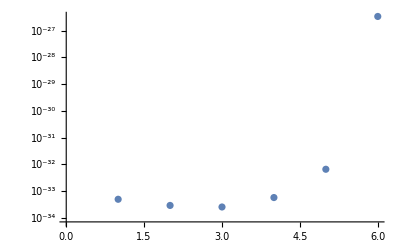

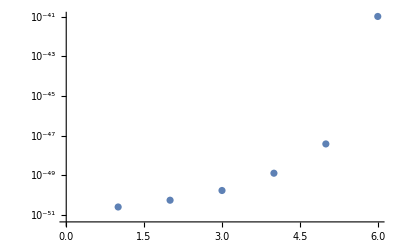

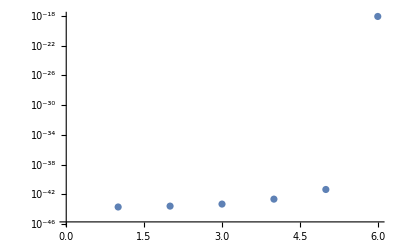

```mathematica
ListLogPlot[{PCApullq10e1[[6]],PCApullq10e2[[6]],PCApullq10e3[[6]],PCApullq10e4[[6]],PCApullq10e5[[6]],PCApullq10e6[[6]]}]
ListLogPlot[{PCAdragq10e1[[6]],PCAdragq10e2[[6]],PCAdragq10e3[[6]],PCAdragq10e4[[6]],PCAdragq10e5[[6]],PCAdragq10e6[[6]]}]
ListLogPlot[{PCAcollessq10e1[[6]],PCAcollessq10e2[[6]],PCAcollessq10e3[[6]],PCAcollessq10e4[[6]],PCAcollessq10e5[[6]],PCAcollessq10e6[[6]]}]
```

```mathematica
datapullq10e4[[1,1]]//MatrixForm
datapullq10e4[[1,1,3;;4,3;;4]]//MatrixForm
```

(6.87237×10^15 | -6.086×10^13 | -503.272 | -4.46366×10^9 | -6.36932×10^14 | -6.02103×10^24
-6.086×10^13 | 9.65004×10^11 | 10.9283 | 6.22338×10^7 | 6.75163×10^12 | 3.90467×10^22
-503.272 | 10.9283 | 2.02814×10^-10 | 0.000712699 | 61.202 | 2.95833×10^11
-4.46366×10^9 | 6.22338×10^7 | 0.000712699 | 4136.93 | 4.71145×10^8 | 3.21115×10^18
-6.36932×10^14 | 6.75163×10^12 | 61.202 | 4.71145×10^8 | 6.20573×10^13 | 5.15539×10^23
-6.02103×10^24 | 3.90467×10^22 | 2.95833×10^11 | 3.21115×10^18 | 5.15539×10^23 | 6.0144×10^33)

(2.02814×10^-10 | 0.000712699
0.000712699 | 4136.93)

```mathematica
LinearSolve[datapullq10e4[[1,1,3;;4,3;;4]],IdentityMatrix[2],Method->"Cholesky"]//MatrixForm
```

(1.2495×10^10 | -2152.61
-2152.61 | 0.00061257)

```mathematica
{vals,vecs}=Eigensystem[datapullq10e4[[1,1]]];
vals
vecs//MatrixForm
```

{6.0144×10^33,1.15292×10^18,3.78854×10^12,1.8878×10^10,4.74965,-2.16999×10^-6}

(-1.0011×10^-9 | 6.4922×10^-12 | 4.91875×10^-23 | 5.3391×10^-16 | 8.57173×10^-11 | 1.
0.996334 | -0.00646128 | -4.89532×10^-14 | -5.31367×10^-7 | -0.0853091 | 1.00479×10^-9
-0.0829039 | -0.319151 | -3.25122×10^-12 | -0.0000156288 | -0.944071 | 0.
0.0211266 | -0.947682 | -4.71029×10^-11 | -0.0000804052 | 0.318517 | 0.
9.32422×10^-7 | -0.0000811899 | 2.11489×10^-6 | 1. | 0.0000108104 | 0.
-1.19761×10^-12 | 1.26031×10^-10 | 1. | -2.11489×10^-6 | -1.09333×10^-11 | 0.)

As an example, for the binary m_1= 10^5 M_sun, m_2= 10 M_sun, with spins χ_1=0.8 and χ_2=0.5, the first principal component (with eigenvalue of order 10^33) can be used to calculate the surrounding density (as indicated by 1 in the upper right corner of the eigenvector matrix).

### Fisher matrix of the waveform difference

Here, we use Ohme et. al’s formulation of the Fisher matrix, for which the inner product of the waveform difference (basically the SNR) is linearized by the Fisher matrix computation.

```mathematica
dhdθdiff[f_,index_]= {ℳ D[hPhBppEVac[f][ℳ,η,χ,τ,ϕ,d](1-Cos[ψenv[f/cc]]),ℳ],
	 η D[hPhBppEVac[f][ℳ,η,χ,τ,ϕ,d](1-Cos[ψenv[f/cc]]),η],
	   D[hPhBppEVac[f][ℳ,η,χ,τ,ϕ,d](1-Cos[ψenv[f/cc]]),τ],
	   D[hPhBppEVac[f][ℳ,η,χ,τ,ϕ,d](1-Cos[ψenv[f/cc]]),ϕ],
D[hPhBppEVac[f][ℳ,η,χ,τ,ϕ,d](1-Cos[ψenv[f/cc]]),χ],
       D[hPhBppEVac[f][ℳ,η,χ,τ,ϕ,d](1-Cos[ψenv[f/cc]]),ρ0]};
```

```mathematica
Fisherdiff[dim_,𝒹_,m1_,m2_,χeff_,index_,env_,ρ0_]:=Block[{ℳ,η,q=m1/m2,d,τ,ϕ,χ,𝒽,𝒽vac,d𝒽,
	ρ,C,𝒫,i,j,Γ,Σ,Noise,fmin,fmax,f,IscoS,𝒯=4,𝒩,amp,ψenv},

Off[NIntegrate::slwcon];
Off[NIntegrate::eincr];

Noise=LISA;
C=Sqrt[5];

(* ---- Creating the vacuum waveform from the input parameters ---- *)
(* ---- Binary parameters q = m1/m2 ≥ 1 ---- *)
{ℳ,η,τ,ϕ,χ,d} = {(q/(1+q)^2)^(3/5)msun (m1+m2),q/(1+q)^2,0,-π/4,χeff,𝒹};
 
(* ---- environmental correction ---- *)
ψenv[f_]=Which[env=="pull",3/(128 (π ℳ f)^(5/3))(m1+m2)^2((m1+m2)f)^index ρ0 G/cc^2,
env=="drag",3/(128 (π ℳ f)^(5/3))(m1+m2)^2((m1+m2)f)^index kβdrag[m1,m2]ρ0 G/cc^2,env=="colless",3/(128 (π ℳ f)^(5/3))(m1+m2)^2((m1+m2)f)^index kβaccretion[m1,m2]ρ0 G/cc^2];

IscoS=cc 𝒻1[(m1+m2)msun,η,χ]+0cc/(π 6^(3/2)(m1+m2)msun); (* PhenomB I-M transition freq *)
amp[f_]=C (2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6); (* Constant amplitude, based only on Subscript[d, L] and chirp mass *)
𝒽[f_] =amp[f] hPhBppE[f/cc][ℳ,η,χ,τ,ϕ,d,ρ0,index];
𝒽vac[f_] =amp[f] hPhBppEVac[f/cc][ℳ,η,χ,τ,ϕ,d];
(*d𝒽[f_] = amp[f]Table[deriv[[i]][f],{i,1,dim}]; *)

d𝒽[f_] = amp[f]dhdθdiff[f/cc,index]; (* differentiated waveform; input for Fisher integral *)

Print["𝒞 = ",C," -- ℳ/M_⊙, = ",ℳ/msun,"-- η = ",N[η]," -- χ_eff = ",χ];

fmin = Max[10^-5,4.149 10^-5 (ℳ/msun 10^-6)^(-5/8) 𝒯^(-3/8)];
fmax = Min[1,IscoS];

(* ---- Signal to noise ratio of the waveform difference ---- *)

ρ = Sqrt[2𝒪[LISA[f],𝒽vac[f](1-Cos[ψenv[f/cc]]),𝒽vac[f],fmin,fmax]];
𝒩 = NIntegrate[f/cc^2/(96/(5π ℳ^2) (π ℳ f/cc)^(11/3)),{f,fmin,fmax}];

Print["PSD = ",LISA," -- [\!\(\*SubscriptBox[\(f\), \(min\)]\),\!\(\*SubscriptBox[\(f\), \(max\)]\)] = [",fmin," , ",fmax,"]Hz -- ρ = ",NumberForm[ρ,6]," -- # cycles = ",𝒩];

(* ---- This a prior on the spin parameters |Subscript[χ, 1,2]|≤1 ---- *)

Γ = ConstantArray[0,{dim,dim}];

(* ---- Compute the Fisher and Covariance Matrix ---- *)

Monitor[For[i=1,i<=dim,i++,
	For[j=1,j<=i,j++,
		Γ[[i,j]] = If[i==j,𝒪[LISA[f],d𝒽[f][[i]],d𝒽[f][[j]],fmin,fmax],
								2𝒪[LISA[f],d𝒽[f][[i]],d𝒽[f][[j]],fmin,fmax]];
		]
	],
	Γ//MatrixForm];

Γ = Normal[Symmetrize[Γ]];

Print["Positive Matrix ? "PositiveDefiniteMatrixQ[Γ]];

Σ=If[PositiveDefiniteMatrixQ[Γ],LinearSolve[Γ,IdentityMatrix[dim],Method->"Cholesky"],Inverse[Γ]];

Return[{Γ,Σ}];

]
```

```mathematica
{m1,m2,χ1,χ2}={10^5,10,0.8,0.5};
χeff=(χ1 m1 + χ2 m2)/(m1+m2);
Fisherdiff[6,1000,m1,m2,χeff,-2,"pull",1000]
```

𝒞 = √5 -- ℳ/M_⊙, = 398.099-- η = 0.00009998 -- χ_eff = 0.79997

PSD = LISA -- [f_min,f_max] = [0.00328985 , 0.113325]Hz -- ρ = 90.8754 -- # cycles = 658378.

NIntegrate::levtime: Time spent solving linear system in LevinRule exceeded 10. seconds. Try increasing the value of the "TimeConstraint" option or decreasing the value of the "Points" option.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

NIntegrate::levtime: Time spent solving linear system in LevinRule exceeded 10. seconds. Try increasing the value of the "TimeConstraint" option or decreasing the value of the "Points" option.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

$Aborted